```mathematica
(*1St Example*)
text =plaintext;
plaintext=Import["https://www.imdb.com/title/tt1333125/reviews?sort=curated&dir=desc&ratingFilter=1"<>ToString@10,"Plaintext"];

Snippet["https://www.imdb.com/title/tt1333125/reviews?sort=curated&dir=desc&ratingFilter=1"] 
WordCloud[DeleteStopwords [text]]

WordCloud[Classify["Sentiment",text]
]
WordCounts[DeleteStopwords [text]]

Snippet["https://www.imdb.com/title/tt1333125/reviews?sort=curated&dir=desc&ratingFilter=1"] 
Classify["Sentiment",text]
```

URL

"https://www.imdb.com/title/tt1333125/reviews?sort=curated&dir=desc&ratingFilter="

CLOUDS OF MOST USED WORDS

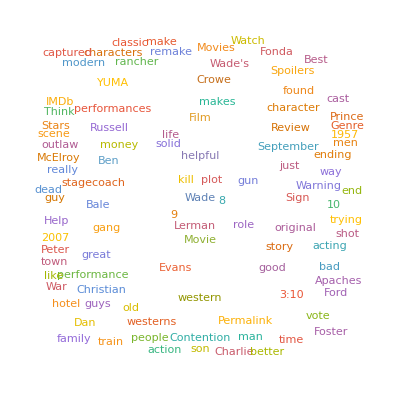

SENTIMENT

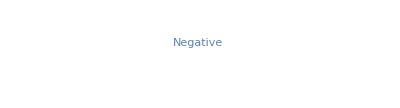

AMOUNTS OF MOST USED WORDS

<|"Wade" -> 76, "film" -> 66, "Evans" -> 53, "movie" -> 52, "helpful" -> 50, "Crowe" -> 48, "Ben" -> 45, "Yuma" -> 42, "good" -> 42, "3:10" -> 41, "Bale" -> 40, "gang" -> 39, "just" -> 38, "western" -> 32, "Russell" -> 31, "10" -> 31, "Dan" -> 28, "review" -> 28, "Sign" -> 28, "bad" -> 27, "original" -> 26, "vote" -> 26, "found" -> 26, "Wade's" -> 25, "Permalink" -> 25, "man" -> 24, "great" -> 24, "character" -> 23, "time" -> 22, "guys" -> 22, "son" -> 21, "westerns" -> 20, "train" -> 20, "Christian" -> 20, "way" -> 18, "rancher" -> 18, "story" -> 18, "Fonda" -> 17, "2007" -> 17, "acting" -> 16, "men" -> 16, "town" -> 15, "best" -> 15, "like" -> 15, "Foster" -> 15, "make" -> 15, "Peter" -> 14, "action" -> 14, "Spoilers" -> 14, "stagecoach" -> 13, "Warning" -> 13, "old" -> 13, "outlaw" -> 13, "remake" -> 13, "guy" -> 13, "performances" -> 12, "help" -> 12, "shot" -> 12, "money" -> 12, "people" -> 12, "ending" -> 12, "Contention" -> 12, "Charlie" -> 12, "1957" -> 12, "Ford" -> 12, "scene" -> 12, "really" -> 12, "modern" -> 12, "kill" -> 11, "think" -> 11, "September" -> 11, "family" -> 11, "characters" -> 11, "McElroy" -> 10, "end" -> 10, "Lerman" -> 10, "gun" -> 10, "Western" -> 10, "makes" -> 10, "role" -> 10, "IMDb" -> 10, "performance" -> 9, "trying" -> 9, "captured" -> 9, "life" -> 9, "hotel" -> 9, "Prince" -> 9, "solid" -> 9, "cast" -> 9, "plot" -> 9, "Stars" -> 9, "Apaches" -> 8, "watch" -> 8, "point" -> 8, "going" -> 8, "movies" -> 8, "Crowe's" -> 8, "scenes" -> 8, "Logan" -> 8, "evil" -> 8, "right" -> 8, "Mangold" -> 8, "James" -> 8, "better" -> 8, "dead" -> 8, "genre" -> 8, "day" -> 8, "9" -> 8, "8" -> 8, "TV" -> 8, "kills" -> 7, "save" -> 7, "know" -> 7, "coach" -> 7, "Heflin" -> 7, "making" -> 7, "want" -> 7, "play" -> 7, "offered" -> 7, "cinematography" -> 7, "leader" -> 7, "fact" -> 7, "War" -> 7, "killer" -> 7, "group" -> 7, "respect" -> 7, "say" -> 7, "station" -> 7, "Van" -> 7, "films" -> 7, "hero" -> 7, "lot" -> 7, "days" -> 7, "Hollywood" -> 7, "Reviews" -> 7, "list" -> 6, "Apparently" -> 6, "$" -> 6, "problem" -> 6, "probably" -> 6, "wife" -> 6, "truly" -> 6, "Westerns" -> 6, "young" -> 6, "mean" -> 6, "version" -> 6, "long" -> 6, "viewer" -> 6, "feel" -> 6, "sense" -> 6, "battle" -> 6, "start" -> 6, "posse" -> 6, "land" -> 6, "gets" -> 6, "played" -> 6, "focus" -> 6, "shoot" -> 6, "nice" -> 6, "actors" -> 6, "screen" -> 6, "2008" -> 6, "father" -> 6, "29" -> 6, "enjoyed" -> 6, "able" -> 6, "shooting" -> 6, "script" -> 6, "things" -> 6, "watching" -> 6, "stop" -> 6, "away" -> 6, "villain" -> 6, "actually" -> 6, "classic" -> 6, "3" -> 6, "created" -> 5, "titles" -> 5, "shoots" -> 5, "gonna" -> 5, "wonderful" -> 5, "stomach" -> 5, "brought" -> 5, "cold" -> 5, "failure" -> 5, "place" -> 5, "seen" -> 5, "look" -> 5, "little" -> 5, "usual" -> 5, "lets" -> 5, "writer" -> 5, "reminiscent" -> 5, "actions" -> 5, "new" -> 5, "Apache" -> 5, "saw" -> 5, "worth" -> 5, "climax" -> 5, "sons" -> 5, "willing" -> 5, "enjoy" -> 5, "completely" -> 5, "left" -> 5, "simply" -> 5, "audience" -> 5, "interesting" -> 5, "quite" -> 5, "losing" -> 5, "Mangold's" -> 5, "throughout" -> 5, "picture" -> 5, "Civil" -> 5, "honest" -> 5, "believe" -> 5, "easy" -> 5, "order" -> 5, "kids" -> 5, "High" -> 5, "outlaws" -> 5, "despite" -> 5, "job" -> 5, "supporting" -> 5, "material" -> 5, "set" -> 5, "run" -> 5, "takes" -> 5, "kind" -> 5, "comes" -> 5, "7" -> 5, "4" -> 5, "1" -> 5, "User" -> 5, "Awards" -> 5, "Movie" -> 5, "Movies" -> 5, "local" -> 4, "menfolk" -> 4, "Crow's" -> 4, "vicious" -> 4, "wait" -> 4, "live" -> 4, "insult" -> 4, "miss" -> 4, "supposed" -> 4, "law" -> 4, "gain" -> 4, "certainly" -> 4, "psychopathic" -> 4, "fan" -> 4, "blood" -> 4, "gives" -> 4, "lives" -> 4, "rescue" -> 4, "territory" -> 4, "terrific" -> 4, "journey" -> 4, "perfect" -> 4, "knew" -> 4, "come" -> 4, "free" -> 4, "surprise" -> 4, "whap" -> 4, "talk" -> 4, "ranch" -> 4, "fine" -> 4, "taken" -> 4, "tension" -> 4, "relationships" -> 4, "die" -> 4, "given" -> 4, "close" -> 4, "escort" -> 4, "far" -> 4, "traditional" -> 4, "Glen" -> 4, "Byron" -> 4, "characterization" -> 4, "stupid" -> 4, "early" -> 4, "conversation" -> 4, "camp" -> 4, "death" -> 4, "psychological" -> 4, "16" -> 4, "brilliant" -> 4, "turns" -> 4, "hand" -> 4, "big" -> 4, "main" -> 4, "lost" -> 4, "impressive" -> 4, "tense" -> 4, "strong" -> 4, "simple" -> 4, "work" -> 4, "reason" -> 4, "bounty" -> 4, "horses" -> 4, "times" -> 4, "minutes" -> 4, "led" -> 4, "thinking" -> 4, "belief" -> 4, "needs" -> 4, "moving" -> 4, "production" -> 4, "struggling" -> 4, "try" -> 4, "teenage" -> 4, "trial" -> 4, "prison" -> 4, "volunteers" -> 4, "goes" -> 4, "Arizona" -> 4, "Bisbee" -> 4, "transport" -> 4, "amoral" -> 4, "mix" -> 4, "heart" -> 4, "West" -> 4, "American" -> 4, "true" -> 4, "21" -> 4, "Noon" -> 4, "Director" -> 4, "thing" -> 4, "fast" -> 4, "turning" -> 4, "rest" -> 4, "top" -> 4, "6" -> 4, "5" -> 4, "Celebs" -> 4, "Festival" -> 4, "Best" -> 4, "News" -> 4, "2021" -> 3, "External" -> 3, "200.00" -> 3, "murdering" -> 3, "enforcement" -> 3, "Crow" -> 3, "team" -> 3, "laughable" -> 3, "open" -> 3, "folks" -> 3, "Gatling" -> 3, "capable" -> 3, "effect" -> 3, "intelligence" -> 3, "viewer's" -> 3, "believable" -> 3, "escape" -> 3, "continue" -> 3, "direction" -> 3, "front" -> 3, "intentions" -> 3, "course" -> 3, "lead" -> 3, "horse" -> 3, "riding" -> 3, "illogical" -> 3, "John" -> 3, "etc" -> 3, "directing" -> 3, "filled" -> 3, "18" -> 3, "fashioned" -> 3, "view" -> 3, "continues" -> 3, "plan" -> 3, "wanted" -> 3, "love" -> 3, "definitely" -> 3, "learn" -> 3, "robbery" -> 3, "stage" -> 3, "members" -> 3, "escorting" -> 3, "carrying" -> 3, "31" -> 3, "knows" -> 3, "maybe" -> 3, "Butterfield" -> 3, "chase" -> 3, "fit" -> 3, "complete" -> 3, "dying" -> 3, "holes" -> 3, "getting" -> 3, "murders" -> 3, "giving" -> 3, "reach" -> 3, "body" -> 3, "satisfying" -> 3, "thought" -> 3, "age" -> 3, "Richard" -> 3, "kept" -> 3, "leave" -> 3, "wrong" -> 3, "feels" -> 3, "taking" -> 3, "face" -> 3, "let" -> 3, "gut" -> 3, "shotgun" -> 3, "fired" -> 3, "updated" -> 3, "loyal" -> 3, "roles" -> 3, "Dan's" -> 3, "landlord" -> 3, "protagonist" -> 3, "Leonard" -> 3, "Elmore" -> 3, "ago" -> 3, "doubt" -> 3, "headed" -> 3, "Henry" -> 3, "hunter" -> 3, "Pinkerton" -> 3, "Tommy" -> 3, "killed" -> 3, "force" -> 3, "attempts" -> 3, "hint" -> 3, "later" -> 3, "use" -> 3, "largely" -> 3, "merely" -> 3, "offer" -> 3, "dialog" -> 3, "events" -> 3, "happened" -> 3, "crew" -> 3, "onto" -> 3, "round" -> 3, "theme" -> 3, "missed" -> 3, "draws" -> 3, "decoy" -> 3, "pay" -> 3, "strengths" -> 3, "totally" -> 3, "morality" -> 3, "disbelief" -> 3, "turn" -> 3, "sit" -> 3, "initially" -> 3, "based" -> 3, "matter" -> 3, "ludicrous" -> 3, "theater" -> 3, "intelligent" -> 3, "happens" -> 3, "Mol" -> 3, "nuanced" -> 3, "pull" -> 3, "failed" -> 3, "older" -> 3, "suddenly" -> 3, "air" -> 3, "guts" -> 3, "except" -> 3, "final" -> 3, "violence" -> 3, "compelling" -> 3, "favorite" -> 3, "admirable" -> 3, "stand" -> 3, "opposite" -> 3, "room" -> 3, "murderous" -> 3, "tries" -> 3, "real" -> 3, "trip" -> 3, "finds" -> 3, "farm" -> 3, "unable" -> 3, "attitude" -> 3, "hard" -> 3, "conscience" -> 3, "charming" -> 3, "deputies" -> 3, "farmer" -> 3, "darkness" -> 3, "Jack" -> 3, "measure" -> 3, "responsible" -> 3, "women" -> 3, "guns" -> 3, "clear" -> 3, "tradition" -> 3, "seeing" -> 3, "Unforgiven" -> 3, "Glenn" -> 3, "idea" -> 3, "Tom" -> 3, "boys" -> 3, "deliver" -> 3, "likes" -> 3, "past" -> 3, "suspenseful" -> 3, "riveting" -> 3, "engaging" -> 3, "expect" -> 3, "dozens" -> 3, "difficult" -> 3, "told" -> 3, "works" -> 3, "leg" -> 3, "crippled" -> 3, "runs" -> 3, "showing" -> 3, "white" -> 3, "YUMA" -> 3, "pairing" -> 3, "potential" -> 3, "2" -> 3, "Review" -> 3, "Film" -> 3, "New" -> 3, "Shows" -> 3, "Popular" -> 3, "250" -> 3, "Top" -> 3, "access" -> 2, "App" -> 2, "lists" -> 2, "Related" -> 2, "Photo" -> 2, "Plot" -> 2, "Credits" -> 2, "Sites" -> 2, "Metacritic" -> 2, "Ratings" -> 2, "FAQ" -> 2, "car" -> 2, "history" -> 2, "DVD" -> 2, "sheriff" -> 2, "townspeople" -> 2, "bunch" -> 2, "Indian" -> 2, "hostile" -> 2, "blank" -> 2, "Country" -> 2, "Ride" -> 2, "Scott" -> 2, "Randolph" -> 2, "Wayne's" -> 2, "ain't" -> 2, "range" -> 2, "surviving" -> 2, "member" -> 2, "thar" -> 2, "AZ" -> 2, "Mabel" -> 2, "law-men" -> 2, "sum" -> 2, "keel" -> 2, "Ahm" -> 2, "200" -> 2, "October" -> 2, "forget" -> 2, "psychopath" -> 2, "Okay" -> 2, "policy" -> 2, "wasted" -> 2, "explosive" -> 2, "opportunities" -> 2, "continually" -> 2, "discussion" -> 2, "despair" -> 2, "crying" -> 2, "buy" -> 2, "realize" -> 2, "crazy" -> 2, "recognize" -> 2, "bodies" -> 2, "movie-making" -> 2, "produced" -> 2, "threatening" -> 2, "faced" -> 2, "ride" -> 2, "price" -> 2, "gray" -> 2, "stops" -> 2, "outruns" -> 2, "ground" -> 2, "damage" -> 2, "blown" -> 2, "easily" -> 2, "degrading" -> 2, "killers" -> 2, "location" -> 2, "pure" -> 2, "fire" -> 2, "Dumb" -> 2, "rides" -> 2, "yeah" -> 2, "plus" -> 2, "slow" -> 2, "continuity" -> 2, "behavior" -> 2, "idiotic" -> 2, "eye" -> 2, "blink" -> 2, "particular" -> 2, "Sure" -> 2, "gone" -> 2, "Cruise" -> 2, "example" -> 2, "hands" -> 2, "sharpshooter" -> 2, "else" -> 2, "justice" -> 2, "using" -> 2, "gritty" -> 2, "complicated" -> 2, "nefarious" -> 2, "debt" -> 2, "nearby" -> 2, "barn" -> 2, "burning" -> 2, "quirky" -> 2, "teen" -> 2, "west" -> 2, "veteran" -> 2, "Bales" -> 2, "subtle" -> 2, "sidekick" -> 2, "remain" -> 2, "impressed" -> 2, "hype" -> 2, "expectations" -> 2, "effort" -> 2, "51" -> 2, "arrogant" -> 2, "dangerous" -> 2, "leaves" -> 2, "risked" -> 2, "explanation" -> 2, "roofs" -> 2, "jumps" -> 2, "situation" -> 2, "Regarding" -> 2, "understand" -> 2, "absolutely" -> 2, "absurd" -> 2, "boss" -> 2, "criminals" -> 2, "offers" -> 2, "instead" -> 2, "cliché" -> 2, "boring" -> 2, "style" -> 2, "bring" -> 2, "actor" -> 2, "got" -> 2, "nomination" -> 2, "Oscar" -> 2, "spectacular" -> 2, "keeps" -> 2, "Peckinpah" -> 2, "directed" -> 2, "beyond" -> 2, "ridiculous" -> 2, "cost" -> 2, "piece" -> 2, "armed" -> 2, "Unfortunately" -> 2, "rail" -> 2, "happy" -> 2, "seemingly" -> 2, "1970s" -> 2, "studios" -> 2, "2011" -> 2, "particularly" -> 2, "Despite" -> 2, "provides" -> 2, "raid" -> 2, "trouble" -> 2, "July" -> 2, "number" -> 2, "wants" -> 2, "couple" -> 2, "cowboys" -> 2, "24" -> 2, "question" -> 2, "eat" -> 2, "Trigger" -> 2, "jumping" -> 2, "Bale's" -> 2, "finishes" -> 2, "gore" -> 2, "producers" -> 2, "case" -> 2, "ogle" -> 2, "chance" -> 2, "words" -> 2, "barmaid" -> 2, "allows" -> 2, "fake" -> 2, "heavy" -> 2, "murder" -> 2, "streets" -> 2, "lots" -> 2, "Gone" -> 2, "badly" -> 2, "prisoner" -> 2, "relatively" -> 2, "modest" -> 2, "projects" -> 2, "17" -> 2, "sure" -> 2, "years" -> 2, "line" -> 2, "started" -> 2, "children" -> 2, "14" -> 2, "plays" -> 2, "cut" -> 2, "oldest" -> 2, "Jones" -> 2, "drunk" -> 2, "Wagon" -> 2, "violent" -> 2, "holdup" -> 2, "Heflin's" -> 2, "driven" -> 2, "previous" -> 2, "Prison" -> 2, "support" -> 2, "liked" -> 2, "Laine" -> 2, "Frankie" -> 2, "Miss" -> 2, "fans" -> 2, "ambiguous" -> 2, "camera" -> 2, "teenager" -> 2, "portrayal" -> 2, "complex" -> 2, "amount" -> 2, "development" -> 2, "allowing" -> 2, "killing" -> 2, "caring" -> 2, "anybody" -> 2, "talent" -> 2, "Tudyk" -> 2, "Alan" -> 2, "step" -> 2, "agent" -> 2, "railroad" -> 2, "accept" -> 2, "notorious" -> 2, "drought" -> 2, "Instead" -> 2, "compare" -> 2, "11" -> 2, "Classic" -> 2, "Remake" -> 2, "Bible" -> 2, "nicely" -> 2, "Richards" -> 2, "Keith" -> 2, "Johnny" -> 2, "second" -> 2, "motivation" -> 2, "orders" -> 2, "follow" -> 2, "genuine" -> 2, "friends" -> 2, "catch" -> 2, "opportunity" -> 2, "sees" -> 2, "laid" -> 2, "comparison" -> 2, "counter" -> 2, "wills" -> 2, "intensity" -> 2, "story's" -> 2, "consider" -> 2, "minds" -> 2, "inside" -> 2, "glimpse" -> 2, "define" -> 2, "layers" -> 2, "core" -> 2, "12" -> 2, "present" -> 2, "delivered" -> 2, "enjoyable" -> 2, "Overall" -> 2, "enjoys" -> 2, "allowed" -> 2, "convincing" -> 2, "forced" -> 2, "drag" -> 2, "keeping" -> 2, "clock" -> 2, "ticking" -> 2, "space" -> 2, "mine" -> 2, "wish" -> 2, "indeed" -> 2, "pressure" -> 2, "aspect" -> 2, "moral" -> 2, "guard" -> 2, "stumbles" -> 2, "arms" -> 2, "war" -> 2, "23" -> 2, "delivery" -> 2, "97" -> 2, "pass" -> 2, "suspend" -> 2, "tired" -> 2, "abet" -> 2, "aid" -> 2, "decides" -> 2, "outside" -> 2, "reputation" -> 2, "heavily" -> 2, "sociopath" -> 2, "escaping" -> 2, "homage" -> 2, "stuck" -> 2, "lacks" -> 2, "plenty" -> 2, "pretty" -> 2, "Gretchen" -> 2, "quality" -> 2, "badman" -> 2, "including" -> 2, "William" -> 2, "interaction" -> 2, "drama" -> 2, "expense" -> 2, "display" -> 2, "period" -> 2, "weapons" -> 2, "film's" -> 2, "ex-soldier" -> 2, "trick" -> 2, "sight" -> 2, "ways" -> 2, "explore" -> 2, "entire" -> 2, "near" -> 2, "realistic" -> 2, "Daves" -> 2, "Delmer" -> 2, "interpretation" -> 2, "sensitive" -> 2, "dignity" -> 2, "issues" -> 2, "stopping" -> 2, "short" -> 2, "understanding" -> 2, "band" -> 2, "paint" -> 2, "fight" -> 2, "criminal" -> 2, "charismatic" -> 2, "impoverished" -> 2, "hide" -> 2, "ruthless" -> 2, "leaving" -> 2, "guards" -> 2, "doomed" -> 2, "dollars" -> 2, "hundred" -> 2, "holds" -> 2, "30" -> 2, "stunning" -> 2, "sacrifice" -> 2, "summer" -> 2, "studio" -> 2, "unscrupulous" -> 2, "imagine" -> 2, "brutal" -> 2, "importantly" -> 2, "court" -> 2, "poor" -> 2, "cash" -> 2, "photographed" -> 2, "beautifully" -> 2, "lieutenant" -> 2, "bit" -> 2, "gunman" -> 2, "Eastwood" -> 2, "post" -> 2, "starters" -> 2, "murderers" -> 2, "weak" -> 2, "dirty" -> 2, "wide" -> 2, "mixture" -> 2, "villains" -> 2, "revisionist" -> 2, "reasons" -> 2, "forever" -> 2, "year" -> 2, "August" -> 2, "Seven" -> 2, "setting" -> 2, "entertaining" -> 2, "highly" -> 2, "exciting" -> 2, "cowboy" -> 2, "grizzled" -> 2, "viewing" -> 2, "suite" -> 2, "bridal" -> 2, "showdown" -> 2, "moments" -> 2, "thoroughly" -> 2, "head" -> 2, "humanity" -> 2, "ends" -> 2, "chief" -> 2, "introduced" -> 2, "excellent" -> 2, "act" -> 2, "stars" -> 2, "powerhouse" -> 2, "central" -> 2, "thanks" -> 2, "manages" -> 2, "January" -> 2, "Star" -> 2, "Rating" -> 2, "title" -> 2, "Yumy" -> 2, "vlak" -> 2, "Español" -> 2, "Français" -> 2, "States" -> 2, "United" -> 2, "supported" -> 2, "Keywords" -> 2, "Help" -> 2, "Central" -> 2, "Toronto" -> 2, "Comic-Con" -> 2, "Winners" -> 2, "Picture" -> 2, "Oscars" -> 2, "Events" -> 2, "Trailers" -> 2, "Watch" -> 2, "Spotlight" -> 2, "India" -> 2, "Showtimes" -> 2, "Office" -> 2, "Box" -> 2, "Genre" -> 2, "Browse" -> 2, "Release" -> 2, "Inc" -> 1, "IMDb.com" -> 1, "1990-2022" -> 1, "©" -> 1, "company" -> 1, "Amazon" -> 1, "Ads" -> 1, "Interest-Based" -> 1, "Policy" -> 1, "Privacy" -> 1, "Use" -> 1, "Conditions" -> 1, "Jobs" -> 1, "Advertising" -> 1, "Room" -> 1, "Press" -> 1, "Developer" -> 1, "Mojo" -> 1, "IMDbPro" -> 1, "Index" -> 1, "Site" -> 1, "Viewed" -> 1, "Recently" -> 1, "Clear" -> 1, "page" -> 1, "Share" -> 1, "related" -> 1, "Jun" -> 1, "04" -> 1, "Bethany" -> 1, "2013" -> 1, "Mar" -> 1, "15" -> 1, "42" -> 1, "Izle" -> 1, "Aug" -> 1, "02" -> 1, "Feb" -> 1, "Crime" -> 1, "months" -> 1, "35" -> 1, "obejrzenia" -> 1, "users" -> 1, "Lists" -> 1, "Create" -> 1, "Explore" -> 1, "Items" -> 1, "Videos" -> 1, "Gallery" -> 1, "Video" -> 1, "Soundtracks" -> 1, "Connections" -> 1, "Versions" -> 1, "Alternate" -> 1, "Quotes" -> 1, "Crazy" -> 1, "Goofs" -> 1, "Trivia" -> 1, "Know" -> 1, "Guide" -> 1, "Parents" -> 1, "Synopsis" -> 1, "Summary" -> 1, "Taglines" -> 1, "Storyline" -> 1, "Specs" -> 1, "Technical" -> 1, "Production" -> 1, "Filming" -> 1, "Company" -> 1, "Official" -> 1, "Dates" -> 1, "Crew" -> 1, "Cast" -> 1, "Details" -> 1, "Opinion" -> 1, "Load" -> 1, "Please" -> 1, "occured" -> 1, "error" -> 1, "decided" -> 1, "standpoint" -> 1, "writing" -> 1, "strictly" -> 1, "project" -> 1, "Given" -> 1, "argued" -> 1, "homestead" -> 1, "Evans's" -> 1, "drawn" -> 1, "incredibly" -> 1, "costumes" -> 1, "passable" -> 1, "fascinating" -> 1, "Extras" -> 1, "eyelash" -> 1, "batting" -> 1, "places" -> 1, "Finally" -> 1, "hitting" -> 1, "regard" -> 1, "fires" -> 1, "cooperates" -> 1, "move" -> 1, "singlehandedly" -> 1, "antics" -> 1, "outraged" -> 1, "citizenry" -> 1, "discover" -> 1, "extras" -> 1, "seconds" -> 1, "surrender" -> 1, "browbeaten" -> 1, "volunteered" -> 1, "pop" -> 1, "cowards" -> 1, "arrive" -> 1, "Evan's" -> 1, "principally" -> 1, "tainted" -> 1, "morally" -> 1, "victims" -> 1, "justified" -> 1, "Somehow" -> 1, "murdered" -> 1, "chugging" -> 1, "aforementioned" -> 1, "burns" -> 1, "chains" -> 1, "drivers" -> 1, "fort" -> 1, "outrun" -> 1, "fresh" -> 1, "defeat" -> 1, "memory" -> 1, "power" -> 1, "mighty" -> 1, "afraid" -> 1, "impressionable" -> 1, "long-winded" -> 1, "diversion" -> 1, "create" -> 1, "transported" -> 1, "march" -> 1, "miscreants" -> 1, "conscript" -> 1, "representative" -> 1, "Railroad's" -> 1, "Pacific" -> 1, "Southern" -> 1, "Grayson" -> 1, "soldiers" -> 1, "Federal" -> 1, "professional" -> 1, "paying" -> 1, "locally" -> 1, "locking" -> 1, "hots" -> 1, "tarries" -> 1, "trapped" -> 1, "apologetically" -> 1, "deeds" -> 1, "witnesses" -> 1, "afar" -> 1, "meets" -> 1, "hostage" -> 1, "dark" -> 1, "Inexplicably" -> 1, "underneath" -> 1, "chivalrous" -> 1, "touchy-feely" -> 1, "heists" -> 1, "outlandish" -> 1, "string" -> 1, "doubles" -> 1, "convincingly" -> 1, "cache" -> 1, "entrusted" -> 1, "misses" -> 1, "hills" -> 1, "match" -> 1, "artillery" -> 1, "machine" -> 1, "new-fangled" -> 1, "equipped" -> 1, "boot" -> 1, "Pinkertons" -> 1, "contracted" -> 1, "crackerjack" -> 1, "protected" -> 1, "cut-throats" -> 1, "soon" -> 1, "credible" -> 1, "rent" -> 1, "evicted" -> 1, "burned" -> 1, "barns" -> 1, "one-legged" -> 1, "Turfseer" -> 1, "Incredulity" -> 1, "338" -> 1, "201" -> 1, "named" -> 1, "bets" -> 1, "Shootist" -> 1, "Howard" -> 1, "Ron" -> 1, "cursing" -> 1, "Bales's" -> 1, "Boone" -> 1, "T" -> 1, "Tall" -> 1, "bantering" -> 1, "quotes" -> 1, "clad" -> 1, "iron" -> 1, "hoping" -> 1, "retain" -> 1, "hopelessness" -> 1, "honorable" -> 1, "righteous" -> 1, "attempt" -> 1, "God" -> 1, "asking" -> 1, "says" -> 1, "thrive" -> 1, "Good" -> 1, "fools" -> 1, "People" -> 1, "message" -> 1, "bigger" -> 1, "trottin" -> 1, "expert" -> 1, "plain" -> 1, "horseback" -> 1, "desert" -> 1, "immediately" -> 1, "removed" -> 1, "bullet" -> 1, "examples" -> 1, "exhibited" -> 1, "type" -> 1, "convince" -> 1, "seriously" -> 1, "frankly" -> 1, "excuse" -> 1, "none" -> 1, "munny" -> 1, "promised" -> 1, "shootin" -> 1, "figures" -> 1, "implications" -> 1, "realizes" -> 1, "finally" -> 1, "hero-worshiping" -> 1, "gunslinging" -> 1, "psychotic" -> 1, "hit" -> 1, "twins" -> 1, "Siamese" -> 1, "ammunition" -> 1, "rounds" -> 1, "firing" -> 1, "theorize" -> 1, "bothers" -> 1, "earn" -> 1, "hiding" -> 1, "Except" -> 1, "daily" -> 1, "stores" -> 1, "wander" -> 1, "atrocity" -> 1, "daylight" -> 1, "broad" -> 1, "gunned" -> 1, "viciously" -> 1, "police" -> 1, "unarmed" -> 1, "barrelhead" -> 1, "dollah" -> 1, "myselves" -> 1, "geet" -> 1, "raffle" -> 1, "mah" -> 1, "Whar's" -> 1, "throwing" -> 1, "custody" -> 1, "holding" -> 1, "earning" -> 1, "simple-minded" -> 1, "Neanderthal" -> 1, "secret" -> 1, "filmmaker" -> 1, "Mr." -> 1, "incarcerated" -> 1, "eagerly" -> 1, "surreptitiously" -> 1, "cahoots" -> 1, "clerk" -> 1, "bartender" -> 1, "20" -> 1, "insights" -> 1, "expansive" -> 1, "ingenuity" -> 1, "content" -> 1, "penance" -> 1, "heaven" -> 1, "high" -> 1, "praise" -> 1, "promote" -> 1, "reviewers" -> 1, "truth" -> 1, "undeniable" -> 1, "robertblanton" -> 1, "1/2" -> 1, "scenario" -> 1, "tend" -> 1, "mangy" -> 1, "brainless" -> 1, "portraying" -> 1, "players" -> 1, "family-predicament" -> 1, "discussing" -> 1, "negated" -> 1, "character-driven" -> 1, "evidence" -> 1, "thin" -> 1, "spread" -> 1, "advance" -> 1, "gun-toting" -> 1, "attack" -> 1, "unturned" -> 1, "degenerates" -> 1, "portrait" -> 1, "sharply-etched" -> 1, "appears" -> 1, "silver-tongued" -> 1, "runaway" -> 1, "yarn" -> 1, "bloodthirsty" -> 1, "hence" -> 1, "basis" -> 1, "Leonard's" -> 1, "fee" -> 1, "gunslinger" -> 1, "Bible-quoting" -> 1, "womanizing" -> 1, "sharp-shooting" -> 1, "join" -> 1, "thrown" -> 1, "deep" -> 1, "Struggling" -> 1, "moonspinner55" -> 1, "second-half" -> 1, "coherency" -> 1, "steam" -> 1, "excitingly" -> 1, "Begins" -> 1, "236" -> 1, "138" -> 1, "absent" -> 1, "guess" -> 1, "shucks" -> 1, "aw" -> 1, "extended" -> 1, "empathize" -> 1, "ridiculousness" -> 1, "absolute" -> 1, "total" -> 1, "terminally" -> 1, "tiny" -> 1, "cranny" -> 1, "nook" -> 1, "blind" -> 1, "sell" -> 1, "citizens" -> 1, "irregularities" -> 1, "repeating" -> 1, "waste" -> 1, "captor" -> 1, "sorry" -> 1, "wanting" -> 1, "forth" -> 1, "fluctuates" -> 1, "shorter" -> 1, "standalone" -> 1, "butchered" -> 1, "so-called" -> 1, "clients" -> 1, "bucks" -> 1, "yank" -> 1, "steal" -> 1, "November" -> 1, "real_hiflyer" -> 1, "refund" -> 1, "checking" -> 1, "ticket" -> 1, "604" -> 1, "354" -> 1, "mess" -> 1, "handcuffed" -> 1, "unmercifully" -> 1, "beaten" -> 1, "heal" -> 1, "mouth" -> 1, "hour" -> 1, "recover" -> 1, "street" -> 1, "risk" -> 1, "psycho" -> 1, "mid" -> 1, "throws" -> 1, "schtick" -> 1, "limb" -> 1, "roaring" -> 1, "spoilers" -> 1, "heads" -> 1, "shaking" -> 1, "laughing" -> 1, "restroom" -> 1, "masses" -> 1, "tomcat91468" -> 1, "awful" -> 1, "Just" -> 1, "177" -> 1, "120" -> 1, "resides" -> 1, "shades" -> 1, "complexities" -> 1, "examining" -> 1, "fertile" -> 1, "Searchers" -> 1, "greats" -> 1, "check" -> 1, "appreciated" -> 1, "spent" -> 1, "appreciate" -> 1, "normally" -> 1, "improvements" -> 1, "old-time" -> 1, "glance" -> 1, "lulls" -> 1, "pace" -> 1, "stunningly" -> 1, "afterward" -> 1, "lively" -> 1, "reined" -> 1, "cleaned" -> 1, "fuel" -> 1, "ample" -> 1, "drive" -> 1, "forces" -> 1, "framework" -> 1, "wider" -> 1, "encourage" -> 1, "receipts" -> 1, "office" -> 1, "box" -> 1, "hopes" -> 1, "owe" -> 1, "suspending" -> 1, "buys" -> 1, "emotional" -> 1, "overly" -> 1, "tends" -> 1, "scare" -> 1, "loved" -> 1, "sister" -> 1, "threw" -> 1, "contrivances" -> 1, "sheen" -> 1, "disturbed" -> 1, "believability" -> 1, "stretches" -> 1, "Towards" -> 1, "mercy" -> 1, "animals" -> 1, "inept" -> 1, "tell" -> 1, "yell" -> 1, "instances" -> 1, "Ultimately" -> 1, "world" -> 1, "old-west" -> 1, "crazed" -> 1, "intensely" -> 1, "held" -> 1, "overboard" -> 1, "mesmerizing" -> 1, "doctor" -> 1, "touch" -> 1, "Widmark" -> 1, "reminded" -> 1, "took" -> 1, "flick" -> 1, "wrapped" -> 1, "study" -> 1, "missing" -> 1, "thankfully" -> 1, "landscape" -> 1, "littering" -> 1, "metaphors" -> 1, "old-fashioned" -> 1, "merging" -> 1, "continuum" -> 1, "obstacles" -> 1, "overwhelming" -> 1, "average" -> 1, "captivating" -> 1, "provide" -> 1, "failings" -> 1, "regrets" -> 1, "bare" -> 1, "revealed" -> 1, "truths" -> 1, "Slowly" -> 1, "intricate" -> 1, "viciousness" -> 1, "childhood" -> 1, "suspect" -> 1, "sensitivity" -> 1, "gentleness" -> 1, "nature" -> 1, "maintaining" -> 1, "shadings" -> 1, "standard" -> 1, "indications" -> 1, "established" -> 1, "depth" -> 1, "bringing" -> 1, "enjoying" -> 1, "Bobby" -> 1, "series" -> 1, "idolize" -> 1, "terms" -> 1, "struggles" -> 1, "father's" -> 1, "doubts" -> 1, "rancher's" -> 1, "youth" -> 1, "separates" -> 1, "circumstances" -> 1, "extraordinary" -> 1, "ultimately" -> 1, "intricacies" -> 1, "showcasing" -> 1, "suspense" -> 1, "inconsistencies" -> 1, "bjxmas" -> 1, "Shades" -> 1, "228" -> 1, "137" -> 1, "reasoning" -> 1, "earlier" -> 1, "yapping" -> 1, "schizo" -> 1, "prove" -> 1, "heap" -> 1, "tops" -> 1, "attempting" -> 1, "insane" -> 1, "especially" -> 1, "door" -> 1, "unfasten" -> 1, "shaky" -> 1, "legged" -> 1, "season" -> 1, "snow" -> 1, "walking" -> 1, "notice" -> 1, "edited" -> 1, "sound" -> 1, "tunnel" -> 1, "drilled" -> 1, "secure" -> 1, "extensive" -> 1, "causing" -> 1, "thereby" -> 1, "bits" -> 1, "tossed" -> 1, "TNT" -> 1, "stack" -> 1, "cuffs" -> 1, "warriors" -> 1, "skills" -> 1, "knives" -> 1, "arrows" -> 1, "sacred" -> 1, "trespassing" -> 1, "fighting" -> 1, "blooded" -> 1, "portray" -> 1, "disguise" -> 1, "caps" -> 1, "feather" -> 1, "wearing" -> 1, "rifles" -> 1, "country" -> 1, "smart" -> 1, "area" -> 1, "rocks" -> 1, "bleeding" -> 1, "slug" -> 1, ".44" -> 1, "hideous" -> 1, "aside" -> 1, "Wow" -> 1, "Easy" -> 1, "ton" -> 1, "weigh" -> 1, "Yeah" -> 1, "lb" -> 1, "+1000" -> 1, "lbs" -> 1, "+3000" -> 1, "armored" -> 1, "dumb" -> 1, "does'nt" -> 1, "director" -> 1, "supervisor" -> 1, "makers" -> 1, "sheer" -> 1, "goofs" -> 1, "numskulled" -> 1, "cloud" -> 1, "scope" -> 1, "explosions" -> 1, "cgi" -> 1, "contradictions" -> 1, "outrageous" -> 1, "Gorbo" -> 1, "502" -> 1, "331" -> 1, "wishing" -> 1, "hours" -> 1, "longing" -> 1, "lover" -> 1, "department" -> 1, "shoulders" -> 1, "carries" -> 1, "deadly" -> 1, "rooting" -> 1, "stellar" -> 1, "drew" -> 1, "non-stop" -> 1, "virtually" -> 1, "luck" -> 1, "down-on" -> 1, "male" -> 1, "alpha" -> 1, "ably" -> 1, "outstanding" -> 1, "due" -> 1, "all" -> 1, "teresa-elbin" -> 1, "93" -> 1, "unexplained" -> 1, "marred" -> 1, "benefiting" -> 1, "firmly" -> 1, "escaped" -> 1, "knock" -> 1, "actively" -> 1, "explain" -> 1, "puzzled" -> 1, "arrives" -> 1, "quickly" -> 1, "change" -> 1, "attacks" -> 1, "fending" -> 1, "safety" -> 1, "minute" -> 1, "Indians" -> 1, "Navajo" -> 1, "flee" -> 1, "inscrutable" -> 1, "shortcoming" -> 1, "movie's" -> 1, "result" -> 1, "terribly" -> 1, "suffered" -> 1, "distracted" -> 1, "fruition" -> 1, "Guy" -> 1, "apparently" -> 1, "sincere" -> 1, "symbiotic" -> 1, "lesser" -> 1, "eyes" -> 1, "anguish" -> 1, "iconic" -> 1, "aim" -> 1, "squinty-eyed" -> 1, "murky" -> 1, "Meanwhile" -> 1, "clutches" -> 1, "untrained" -> 1, "upper" -> 1, "mental" -> 1, "mind" -> 1, "goals" -> 1, "charmlessly" -> 1, "coldly" -> 1, "bullets" -> 1, "gunplay" -> 1, "grab" -> 1, "hell" -> 1, "unabated" -> 1, "geographical" -> 1, "precious" -> 1, "gambit" -> 1, "schlep" -> 1, "trail" -> 1, "varmints" -> 1, "lure" -> 1, "Luckily" -> 1, "trundled" -> 1, "fearless" -> 1, "Ah" -> 1, "decision" -> 1, "ungrateful" -> 1, "Saddled" -> 1, "spineless" -> 1, "thinks" -> 1, "tuberculosis" -> 1, "sick" -> 1, "payment" -> 1, "titular" -> 1, "escorted" -> 1, "robber" -> 1, "property" -> 1, "river" -> 1, "damming" -> 1, "owner" -> 1, "foreclosed" -> 1, "farm's" -> 1, "dirt-poor" -> 1, "means" -> 1, "dastardly" -> 1, "mystery" -> 1, "nebulous" -> 1, "scratching" -> 1, "noble" -> 1, "playes" -> 1, "motives" -> 1, "morals" -> 1, "skillfully" -> 1, "leads" -> 1, "craftiness" -> 1, "earnest" -> 1, "serviceable" -> 1, "oater" -> 1, "dfranzen70" -> 1, "wanna" -> 1, "548" -> 1, "422" -> 1, "dysfunctional" -> 1, "slices" -> 1, "comedies" -> 1, "dumbed" -> 1, "era" -> 1, "anymore" -> 1, "respects" -> 1, "majesty" -> 1, "expanse" -> 1, "captures" -> 1, "beautiful" -> 1, "consistently" -> 1, "ranks" -> 1, "Cinematically" -> 1, "recognizes" -> 1, "eventually" -> 1, "drudge" -> 1, "disillusioned" -> 1, "Initially" -> 1, "accolades" -> 1, "deserves" -> 1, "hidden" -> 1, "demonstrate" -> 1, "Iy" -> 1, "pathos" -> 1, "beleaguered" -> 1, "infuses" -> 1, "taste" -> 1, "Pirate" -> 1, "Depp" -> 1, "affected" -> 1, "Foster's" -> 1, "constant" -> 1, "duly" -> 1, "received" -> 1, "directorial" -> 1, "Line" -> 1, "Walking" -> 1, "indifferent" -> 1, "Bunch" -> 1, "Wild" -> 1, "Shane" -> 1, "exceptions" -> 1, "International" -> 1, "preview" -> 1, "night" -> 1, "harricks" -> 1, "Indomitable" -> 1, "Indomáveis" -> 1, "Os" -> 1, "Brazil" -> 1, "Title" -> 1, "five" -> 1, "Maybe" -> 1, "incidental" -> 1, "cruel" -> 1, "foot" -> 1, "survival" -> 1, "perspective" -> 1, "dreadful" -> 1, "siege" -> 1, "compatible" -> 1, "corruption" -> 1, "ok" -> 1, "accepts" -> 1, "neither" -> 1, "raise" -> 1, "alleys" -> 1, "corny" -> 1, "ridiculously" -> 1, "feelings" -> 1, "Hollywoodian" -> 1, "top-notch" -> 1, "marketing" -> 1, "positive" -> 1, "influenced" -> 1, "viewers" -> 1, "Indeed" -> 1, "overrated" -> 1, "incoherent" -> 1, "deceptive" -> 1, "follows" -> 1, "closer" -> 1, "200,00" -> 1, "receive" -> 1, "return" -> 1, "sent" -> 1, "PM" -> 1, "city" -> 1, "heist" -> 1, "powerful" -> 1, "large" -> 1, "owing" -> 1, "broken" -> 1, "Daniel" -> 1, "claudio_carvalho" -> 1, "Overrated" -> 1, "Incoherent" -> 1, "Corny" -> 1, "Absurd" -> 1, "162" -> 1, "100" -> 1, "Wayne" -> 1, "Cooper" -> 1, "Gary" -> 1, "Clint" -> 1, "music" -> 1, "level" -> 1, "excellence" -> 1, "sceneries" -> 1, "amazing" -> 1, "entertained" -> 1, "carried" -> 1, "trap" -> 1, "fall" -> 1, "effects" -> 1, "length" -> 1, "talky" -> 1, "heard" -> 1, "deserved" -> 1, "purpose" -> 1, "willingness" -> 1, "desperation" -> 1, "displays" -> 1, "verge" -> 1, "Christain" -> 1, "worthy" -> 1, "joy" -> 1, "mystique" -> 1, "shock" -> 1, "putting" -> 1, "delivers" -> 1, "overlooked" -> 1, "superb" -> 1, "February" -> 1, "alexkolokotronis" -> 1, "Modern" -> 1, "1980s" -> 1, "radical" -> 1, "ethos" -> 1, "Sam" -> 1, "it'd" -> 1, "mini-masterpiece" -> 1, "sort" -> 1, "wise" -> 1, "Narrative" -> 1, "climatic" -> 1, "confused" -> 1, "mentor" -> 1, "forgetting" -> 1, "Prnce" -> 1, "blame" -> 1, "Considering" -> 1, "honour" -> 1, "code" -> 1, "motivated" -> 1, "painted" -> 1, "warped" -> 1, "bys" -> 1, "passer" -> 1, "innocent" -> 1, "okay" -> 1, "Let" -> 1, "empathy" -> 1, "gold" -> 1, "emphasise" -> 1, "asked" -> 1, "cake" -> 1, "reaches" -> 1, "release" -> 1, "federal" -> 1, "Wadee" -> 1, "fugitive" -> 1, "revolves" -> 1, "anti-Western" -> 1, "uneasy" -> 1, "endings" -> 1, "audiences" -> 1, "decades" -> 1, "survived" -> 1, "concept" -> 1, "limited" -> 1, "hindsight" -> 1, "odds" -> 1, "whatever" -> 1, "win" -> 1, "distinction" -> 1, "known" -> 1, "Previously" -> 1, "lines" -> 1, "blurred" -> 1, "shockingly" -> 1, "BUNCH" -> 1, "WILD" -> 1, "success" -> 1, "commercial" -> 1, "critical" -> 1, "amongst" -> 1, "favour" -> 1, "fell" -> 1, "Robertson" -> 1, "Theo" -> 1, "Morality" -> 1, "Dubious" -> 1, "recommend" -> 1, "form" -> 1, "Cristian" -> 1, "unapologetic" -> 1, "ambiguity" -> 1, "degree" -> 1, "slightly" -> 1, "gunfight" -> 1, "pieces" -> 1, "lessen" -> 1, "compares" -> 1, "interested" -> 1, "determined" -> 1, "well-armed" -> 1, "renegade" -> 1, "occupied" -> 1, "Needing" -> 1, "wages" -> 1, "railway" -> 1, "gangsters" -> 1, "letting" -> 1, "fears" -> 1, "financial" -> 1, "centred" -> 1, "2019" -> 1, "Tweekums" -> 1, "50" -> 1, "10/10" -> 1, "fantastic" -> 1, "recommending" -> 1, "guaranteed" -> 1, "unforgiven" -> 1, "ugly" -> 1, "rank" -> 1, "year's" -> 1, "convinced" -> 1, "Doc" -> 1, "Ben's" -> 1, "brings" -> 1, "ask" -> 1, "policemen" -> 1, "swinger" -> 1, "fastest" -> 1, "thief" -> 1, "nominated" -> 1, "surprised" -> 1, "incredible" -> 1, "surrounding" -> 1, "casting" -> 1, "complaint" -> 1, "rating" -> 1, "feeling" -> 1, "awesome" -> 1, "clicked" -> 1, "afternoon" -> 1, "picked" -> 1, "Smells_Like_Cheese" -> 1, "Brit" -> 1, "Austrailian" -> 1, "legitimate" -> 1, "bankrupt" -> 1, "ideas" -> 1, "Hollywood's" -> 1, "portfolio" -> 1, "nickel" -> 1, "Reeves" -> 1, "Keanu" -> 1, "Son" -> 1, "Rogers" -> 1, "Roy" -> 1, "sock" -> 1, "one-size-fits" -> 1, "narrative" -> 1, "retained" -> 1, "bloody" -> 1, "stoicism" -> 1, "deadpan" -> 1, "remorse" -> 1, "cell" -> 1, "barred" -> 1, "climbing" -> 1, "aboard" -> 1, "parody" -> 1, "self" -> 1, "cascade" -> 1, "Unlike" -> 1, "rope" -> 1, "saved" -> 1, "instantly" -> 1, "whirls" -> 1, "epiphany" -> 1, "Looking" -> 1, "teenaged" -> 1, "plugged" -> 1, "visited" -> 1, "Territorial" -> 1, "ended" -> 1, "relief" -> 1, "sigh" -> 1, "designed" -> 1, "bloodletting" -> 1, "fix" -> 1, "periodic" -> 1, "violence-hungry" -> 1, "pandering" -> 1, "disgusting" -> 1, "fork" -> 1, "stolen" -> 1, "chest" -> 1, "stabs" -> 1, "figure" -> 1, "sleeping" -> 1, "creeps" -> 1, "captives" -> 1, "nude" -> 1, "bedroom" -> 1, "Shaw" -> 1, "Vinessa" -> 1, "replacement" -> 1, "Farr's" -> 1, "bed" -> 1, "Farr" -> 1, "Felicia" -> 1, "charm" -> 1, "toes" -> 1, "longer" -> 1, "pinky" -> 1, "extra" -> 1, "counting" -> 1, "fingers" -> 1, "ten" -> 1, "count" -> 1, "killings" -> 1, "multiple" -> 1, "startling" -> 1, "abject" -> 1, "image" -> 1, "lynching" -> 1, "lobby" -> 1, "neck" -> 1, "hanged" -> 1, "helper" -> 1, "hapless" -> 1, "gruesome" -> 1, "fairly" -> 1, "deliberate" -> 1, "prefer" -> 1, "unpretentious" -> 1, "resembled" -> 1, "Old" -> 1, "historic" -> 1, "news" -> 1, "necessarily" -> 1, "grim" -> 1, "looks" -> 1, "winter" -> 1, "Mexico" -> 1, "northern" -> 1, "Angeles" -> 1, "Los" -> 1, "ranches" -> 1, "imitation" -> 1, "dusty" -> 1, "sunny" -> 1, "familiar" -> 1, "adhered" -> 1, "conventions" -> 1, "language" -> 1, "filthier" -> 1, "characterized" -> 1, "dirtier" -> 1, "muddier" -> 1, "sadistic" -> 1, "bloodier" -> 1, "sexier" -> 1, "word" -> 1, "Currently" -> 1, "gargantuan" -> 1, "rifacimento" -> 1, "collects" -> 1, "carefree" -> 1, "successfully" -> 1, "1950s" -> 1, "budget" -> 1, "low" -> 1, "black-and-white" -> 1, "loneliness" -> 1, "greenlight" -> 1, "MBAs" -> 1, "remark" -> 1, "thirty-year-old" -> 1, "borrow" -> 1, "tempted" -> 1, "imitations" -> 1, "remakes" -> 1, "2009" -> 1, "June" -> 1, "19" -> 1, "rmax304823" -> 1, "26" -> 1, "grandparents" -> 1, "grandfather" -> 1, "Harve's" -> 1, "dramas" -> 1, "commend" -> 1, "mentions" -> 1, "interview" -> 1, "Riders" -> 1, "Bull" -> 1, "Professional" -> 1, "Texas" -> 1, "Stephenville" -> 1, "Stewart" -> 1, "Harve" -> 1, "dedicated" -> 1, "affections" -> 1, "gratuitous" -> 1, "expected" -> 1, "somewhat" -> 1, "thug" -> 1, "Jaeckel" -> 1, "punk" -> 1, "Added" -> 1, "bribe" -> 1, "legacy" -> 1, "outcome" -> 1, "experience" -> 1, "shared" -> 1, "bond" -> 1, "Dad" -> 1, "tags" -> 1, "Young" -> 1, "wife's" -> 1, "conversely" -> 1, "built" -> 1, "moved" -> 1, "speech" -> 1, "heartfelt" -> 1, "responds" -> 1, "pleads" -> 1, "Dana" -> 1, "Leora" -> 1, "wrenching" -> 1, "services" -> 1, "volunteer" -> 1, "eliminated" -> 1, "overpowered" -> 1, "momentarily" -> 1, "affair" -> 1, "hardly" -> 1, "greatest" -> 1, "considered" -> 1, "rogue" -> 1, "sly" -> 1, "Ford's" -> 1, "substitutes" -> 1, "fateful" -> 1, "boarding" -> 1, "capture" -> 1, "State" -> 1, "agrees" -> 1, "caught" -> 1, "ordinary" -> 1, "echoed" -> 1, "song" -> 1, "singing" -> 1, "fifties" -> 1, "bkoganbing" -> 1, "210" -> 1, "128" -> 1, "recommended" -> 1, "Highly" -> 1, "ironic" -> 1, "surprising" -> 1, "establishing" -> 1, "gun-fight" -> 1, "build" -> 1, "used" -> 1, "medium" -> 1, "accurate" -> 1, "unusually" -> 1, "polar" -> 1, "protégé" -> 1, "nihilistic" -> 1, "equally" -> 1, "unpredictable" -> 1, "wily" -> 1, "stares" -> 1, "meaningful" -> 1, "coupled" -> 1, "tremendous" -> 1, "dominate" -> 1, "drawing" -> 1, "achieves" -> 1, "drop" -> 1, "impossible" -> 1, "shoot-em-ups" -> 1, "studies" -> 1, "straightforward" -> 1, "showcases" -> 1, "transition" -> 1, "talented" -> 1, "engaged" -> 1, "stood" -> 1, "dogs" -> 1, "Eventually" -> 1, "eldest" -> 1, "connection" -> 1, "whimsically" -> 1, "confront" -> 1, "paths" -> 1, "cross" -> 1, "merciless" -> 1, "suffering" -> 1, "family-man" -> 1, "would" -> 1, "respectively" -> 1, "antagonist" -> 1, "suspension" -> 1, "willful" -> 1, "permit" -> 1, "background" -> 1, "gave" -> 1, "exclusively" -> 1, "remember" -> 1, "featuring" -> 1, "Long" -> 1, "mstomaso" -> 1, "Enjoyable" -> 1, "Thoroughly" -> 1, "45" -> 1, "unbelievable" -> 1, "reading" -> 1, "single" -> 1, "passages" -> 1, "quote" -> 1, "career" -> 1, "siding" -> 1, "agree" -> 1, "Morricone" -> 1, "Ennio" -> 1, "1970's" -> 1, "spaghetti" -> 1, "sounding" -> 1, "score" -> 1, "musical" -> 1, "comment" -> 1, "throw" -> 1, "appeared" -> 1, "late" -> 1, "suggestive" -> 1, "aged" -> 1, "Fonda's" -> 1, "Sparrow" -> 1, "Depp's" -> 1, "command" -> 1, "Speaking" -> 1, "cause" -> 1, "factor" -> 1, "admiration" -> 1, "strongly" -> 1, "suggest" -> 1, "listen" -> 1, "finale" -> 1, "dismissal" -> 1, "intemperate" -> 1, "lies" -> 1, "Therein" -> 1, "boss's" -> 1, "add" -> 1, "Tommy's" -> 1, "payroll" -> 1, "robbed" -> 1, "inspecting" -> 1, "thorough" -> 1, "refer" -> 1, "insight" -> 1, "needing" -> 1, "Yes" -> 1, "asks" -> 1, "declines" -> 1, "light" -> 1, "conspiring" -> 1, "hold" -> 1, "implores" -> 1, "engage" -> 1, "tick" -> 1, "bodyguard" -> 1, "outlaw's" -> 1, "fundamental" -> 1, "ambush" -> 1, "payback" -> 1, "coolie" -> 1, "certain" -> 1, "saves" -> 1, "occurred" -> 1, "lesson" -> 1, "teach" -> 1, "duty" -> 1, "mission" -> 1, "reasonable" -> 1, "fully" -> 1, "proving" -> 1, "resolve" -> 1, "obsessive" -> 1, "senior" -> 1, "developing" -> 1, "important" -> 1, "proves" -> 1, "addition" -> 1, "position" -> 1, "secondary" -> 1, "occupying" -> 1, "entirely" -> 1, "foes" -> 1, "respective" -> 1, "employ" -> 1, "battles" -> 1, "substantially" -> 1, "differs" -> 1, "sudden" -> 1, "clues" -> 1, "occur" -> 1, "fail" -> 1, "dismiss" -> 1, "protagonists" -> 1, "offering" -> 1, "crafted" -> 1, "finely" -> 1, "adding" -> 1, "presented" -> 1, "themes" -> 1, "building" -> 1, "surpasses" -> 1, "re-makes" -> 1, "rare" -> 1, "convinces" -> 1, "masterfully" -> 1, "crafts" -> 1, "name" -> 1, "Utilizing" -> 1, "classicsoncall" -> 1, "Pa" -> 1, "aspects" -> 1, "Support" -> 1, "memorable" -> 1, "demands" -> 1, "device" -> 1, "desire" -> 1, "added" -> 1, "playing" -> 1, "felt" -> 1, "selling" -> 1, "star" -> 1, "shots" -> 1, "tighter" -> 1, "locations" -> 1, "landscapes" -> 1, "sweeping" -> 1, "obligated" -> 1, "regards" -> 1, "restrained" -> 1, "succeeds" -> 1, "sterling" -> 1, "disagree" -> 1, "needless" -> 1, "currently" -> 1, "cooker" -> 1, "tending" -> 1, "effectively" -> 1, "albeit" -> 1, "majority" -> 1, "smaller" -> 1, "waiting" -> 1, "occurs" -> 1, "tale" -> 1, "values" -> 1, "attracted" -> 1, "simplicity" -> 1, "figured" -> 1, "commented" -> 1, "greatly" -> 1, "cinema" -> 1, "sets" -> 1, "joins" -> 1, "bar" -> 1, "debts" -> 1, "landowner" -> 1, "refusal" -> 1, "longs" -> 1, "amputee" -> 1, "dare" -> 1, "pushed" -> 1, "April" -> 1, "moo" -> 1, "bob" -> 1, "board" -> 1, "66" -> 1, "probability" -> 1, "insults" -> 1, "Hood" -> 1, "Robin" -> 1, "conversion" -> 1, "latter" -> 1, "serious" -> 1, "pissing" -> 1, "gauntlet" -> 1, "running" -> 1, "upside" -> 1, "half" -> 1, "targets" -> 1, "sitting" -> 1, "bunched" -> 1, "holed" -> 1, "atop" -> 1, "sits" -> 1, "seven" -> 1, "standing" -> 1, "signaling" -> 1, "invincible" -> 1, "diminishes" -> 1, "recaptured" -> 1, "bound" -> 1, "hardened" -> 1, "supposedly" -> 1, "escapes" -> 1, "clever" -> 1, "fiendishly" -> 1, "notion" -> 1, "crimp" -> 1, "puts" -> 1, "stupidity" -> 1, "fluke" -> 1, "recapturing" -> 1, "satisfactorily" -> 1, "fleshes" -> 1, "fair" -> 1, "twenty" -> 1, "SPOILER" -> 1, "nose" -> 1, "pleasure" -> 1, "base" -> 1, "bothersome" -> 1, "concentration" -> 1, "attention" -> 1, "lazy" -> 1, "pander" -> 1, "deciding" -> 1, "Simple" -> 1, "screw" -> 1, "man's" -> 1, "posturing" -> 1, "theatric" -> 1, "Great" -> 1, "Granted" -> 1, "adolescence" -> 1, "dreamy" -> 1, "treats" -> 1, "rational" -> 1, "semblance" -> 1, "allow" -> 1, "plotting" -> 1, "nowadays" -> 1, "hooks" -> 1, "obvious" -> 1, "comments" -> 1, "Reading" -> 1, "ikanboy" -> 1, "ruined" -> 1, "252" -> 1, "163" -> 1, "exited" -> 1, "Think" -> 1, "conventional" -> 1, "flawless" -> 1, "imitating" -> 1, "art" -> 1, "Talk" -> 1, "wonderfully" -> 1, "episodes" -> 1, "generous" -> 1, "constantly" -> 1, "delve" -> 1, "flicks" -> 1, "spared" -> 1, "suppose" -> 1, "elements" -> 1, "wonder" -> 1, "clothing" -> 1, "injuries" -> 1, "wagons" -> 1, "dirt" -> 1, "sensibility" -> 1, "welcome" -> 1, "preoccupation" -> 1, "Courage" -> 1, "care" -> 1, "marginal" -> 1, "key" -> 1, "reality" -> 1, "Peck" -> 1, "Gregory" -> 1, "generation's" -> 1, "dawned" -> 1, "Russel" -> 1, "speak" -> 1, "clearing" -> 1, "socrates99" -> 1, "Reminds" -> 1, "141" -> 1, "101" -> 1, "inevitable" -> 1, "photography" -> 1, "breathtaking" -> 1, "sequences" -> 1, "lately" -> 1, "inhabit" -> 1, "comfortably" -> 1, "misunderstood" -> 1, "splendid" -> 1, "parts" -> 1, "smooth-talking" -> 1, "cold-blooded" -> 1, "gifted" -> 1, "teases" -> 1, "integrity" -> 1, "virtue" -> 1, "relation" -> 1, "virtues" -> 1, "celebrate" -> 1, "appreciation" -> 1, "develops" -> 1, "robbers" -> 1, "endearing" -> 1, "poignant" -> 1, "unforgettable" -> 1, "destiny" -> 1, "unknown" -> 1, "concentrates" -> 1, "son's" -> 1, "regain" -> 1, "City" -> 1, "perilous" -> 1, "undertake" -> 1, "quantity" -> 1, "admires" -> 1, "disappointment" -> 1, "efforts" -> 1, "humiliated" -> 1, "protect" -> 1, "injury" -> 1, "Beaten" -> 1, "bandit" -> 1, "enigmatic" -> 1, "March" -> 1, "Nazi_Fighter_David" -> 1, "accident" -> 1, "courageous" -> 1, "493" -> 1, "360" -> 1, "romance" -> 1, "electric" -> 1, "rough-hewn" -> 1, "ups" -> 1, "shoot-em" -> 1, "straight" -> 1, "golden" -> 1, "relive" -> 1, "modicum" -> 1, "dog" -> 1, "winner" -> 1, "dump" -> 1, "extremely" -> 1, "smile" -> 1, "roguish" -> 1, "alternately" -> 1, "working" -> 1, "psychologically" -> 1, "pursuit" -> 1, "hot" -> 1, "task" -> 1, "Getting" -> 1, "via" -> 1, "murderer" -> 1, "helping" -> 1, "home-saving" -> 1, "pickup" -> 1, "nail-bitingly" -> 1, "Dog" -> 1, "Alpha" -> 1, "Palance" -> 1, "Cleef" -> 1, "Lee" -> 1, "baddie" -> 1, "certifiable" -> 1, "Delightfully" -> 1, "cowardice" -> 1, "equal" -> 1, "wee" -> 1, "clash" -> 1, "angst-filled" -> 1, "juxtaposed" -> 1, "profession" -> 1, "reflections" -> 1, "philosophical" -> 1, "ratchet" -> 1, "marginalized" -> 1, "cusp" -> 1, "cunning" -> 1, "lawmen" -> 1, "towns" -> 1, "prairies" -> 1, "heroes" -> 1, "19th-century" -> 1, "forms" -> 1, "heroic" -> 1, "excited" -> 1, "Dead" -> 1, "Quick" -> 1, "pleasant" -> 1, "converge" -> 1, "specific" -> 1, "arriving" -> 1, "Magnificent" -> 1, "references" -> 1, "Sawyer" -> 1, "Adventures" -> 1, "Twain's" -> 1, "Mark" -> 1, "President" -> 1, "Forest" -> 1, "Sherwood" -> 1, "said" -> 1, "loss" -> 1, "compensate" -> 1, "claim" -> 1, "civilization" -> 1, "wondering" -> 1, "grieving" -> 1, "went" -> 1, "accoutrements" -> 1, "hid" -> 1, "dressed" -> 1, "jdesando" -> 1, "33" -> 1, "masterful" -> 1, "familiarity" -> 1, "craft" -> 1, "master" -> 1, "shows" -> 1, "LAND" -> 1, "COP" -> 1, "proved" -> 1, "hateable" -> 1, "creepy" -> 1, "unrecognisable" -> 1, "edge-of-the-seat" -> 1, "tremendously" -> 1, "futures" -> 1, "decide" -> 1, "fate" -> 1, "ponder" -> 1, "assorted" -> 1, "hotel's" -> 1, "favourite" -> 1, "chases" -> 1, "quiet" -> 1, "creating" -> 1, "choreographed" -> 1, "expertly" -> 1, "hi-tech" -> 1, "showdowns" -> 1, "exploding" -> 1, "shoot-outs" -> 1, "successful" -> 1, "similarly" -> 1, "TERMINATOR" -> 1, "BOURNE" -> 1, "achieve" -> 1, "paced" -> 1, "human" -> 1, "deeply" -> 1, "caricature" -> 1, "flawed" -> 1, "black" -> 1, "B-movie" -> 1, "Clearly" -> 1, "unmissable" -> 1, "game" -> 1, "actor's" -> 1, "RANGE" -> 1, "OPEN" -> 1, "Costner's" -> 1, "genre's" -> 1, "reminds" -> 1, "2015" -> 1, "Leofwine_draca" -> 1, "Filter" -> 1, "Reviewer" -> 1, "Prolific" -> 1, "Votes" -> 1, "Total" -> 1, "Date" -> 1, "Featured" -> 1, "Sort" -> 1, "Hide" -> 1, "690" -> 1, "México" -> 1, "España" -> 1, "Brasil" -> 1, "Português" -> 1, "Italia" -> 1, "Italiano" -> 1, "भारत" -> 1, "हिंदी" -> 1, "Deutschland" -> 1, "Deutsch" -> 1, "France" -> 1, "Canada" -> 1, "Partially" -> 1, "English" -> 1, "Fully" -> 1, "EN" -> 1, "Watchlist" -> 1, "Search" -> 1, "Advanced" -> 1, "Companies" -> 1, "Episodes" -> 1, "Titles" -> 1, "Professionals" -> 1, "Industry" -> 1, "Polls" -> 1, "Zone" -> 1, "Contributor" -> 1, "Center" -> 1, "Community" -> 1, "Celebrity" -> 1, "Today" -> 1, "Born" -> 1, "Int'l" -> 1, "Sundance" -> 1, "York" -> 1, "Diego" -> 1, "San" -> 1, "STARmeter" -> 1, "Emmys" -> 1, "2022" -> 1, "Podcasts" -> 1, "Picks" -> 1, "Originals" -> 1, "Latest" -> 1, "Streaming" -> 1, "Tickets" -> 1, "Calendar" -> 1, "Menu" -> 1|>

https://www.imdb.com/title/tt1333125/reviews?sort=curated&dir=desc&ratingFilter=

Negative

urL

"https://www.imdb.com/title/tt1333125/reviews?sort=curated&dir=desc&ratingFilter="

CLOUDS OF MOST USED WORDS

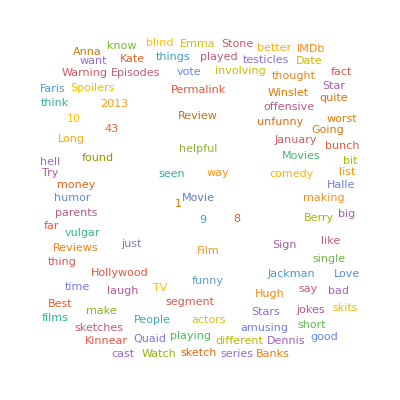

SENTIMENT

-Graphics-

AMOUNT OF MOST USED WORDS

<|"film" -> 59, "helpful" -> 50, "movie" -> 50, "Movie" -> 50, "43" -> 45, "just" -> 35, "funny" -> 32, "review" -> 31, "10" -> 29, "Sign" -> 28, "found" -> 27, "Permalink" -> 25, "vote" -> 25, "2013" -> 23, "like" -> 22, "1" -> 20, "segment" -> 18, "Jackman" -> 18, "actors" -> 18, "laugh" -> 17, "make" -> 17, "Hugh" -> 17, "Kate" -> 16, "time" -> 16, "movies" -> 15, "comedy" -> 15, "say" -> 15, "Winslet" -> 14, "seen" -> 14, "Hollywood" -> 13, "way" -> 13, "bad" -> 12, "date" -> 12, "short" -> 12, "want" -> 12, "humor" -> 12, "stars" -> 11, "unfunny" -> 11, "blind" -> 11, "offensive" -> 11, "January" -> 11, "sketches" -> 10, "people" -> 10, "star" -> 10, "Berry" -> 10, "Halle" -> 10, "vulgar" -> 10, "fact" -> 9, "skits" -> 9, "think" -> 9, "money" -> 9, "Stone" -> 9, "Emma" -> 9, "Faris" -> 9, "Anna" -> 9, "Quaid" -> 9, "jokes" -> 9, "Stars" -> 9, "IMDb" -> 9, "worst" -> 8, "far" -> 8, "series" -> 8, "good" -> 8, "playing" -> 8, "list" -> 8, "different" -> 8, "quite" -> 8, "played" -> 8, "things" -> 8, "thing" -> 8, "Dennis" -> 8, "cast" -> 8, "know" -> 8, "Spoilers" -> 8, "sketch" -> 7, "try" -> 7, "amusing" -> 7, "single" -> 7, "making" -> 7, "testicles" -> 7, "better" -> 7, "hell" -> 7, "thought" -> 7, "involving" -> 7, "Kinnear" -> 7, "films" -> 7, "Warning" -> 7, "8" -> 7, "Reviews" -> 7, "TV" -> 7, "crap" -> 6, "episodes" -> 6, "showing" -> 6, "experience" -> 6, "watching" -> 6, "cat" -> 6, "Watts" -> 6, "Naomi" -> 6, "love" -> 6, "going" -> 6, "bit" -> 6, "bunch" -> 6, "trailer" -> 6, "worse" -> 6, "best" -> 6, "watched" -> 6, "really" -> 6, "work" -> 6, "Banks" -> 6, "directors" -> 6, "disgusting" -> 6, "Gere" -> 6, "Richard" -> 6, "poop" -> 6, "Chris" -> 6, "watch" -> 6, "Greg" -> 6, "story" -> 6, "point" -> 6, "laughs" -> 6, "real" -> 6, "9" -> 6, "Movies" -> 6, "created" -> 5, "titles" -> 5, "20" -> 5, "raunchy" -> 5, "great" -> 5, "wants" -> 5, "pair" -> 5, "Liev" -> 5, "long" -> 5, "said" -> 5, "simply" -> 5, "actually" -> 5, "got" -> 5, "American" -> 5, "28" -> 5, "segments" -> 5, "stories" -> 5, "makes" -> 5, "lot" -> 5, "maybe" -> 5, "June" -> 5, "Elizabeth" -> 5, "dare" -> 5, "team" -> 5, "basketball" -> 5, "Long" -> 5, "Justin" -> 5, "woman" -> 5, "iBabe" -> 5, "Culkin" -> 5, "goes" -> 5, "couple" -> 5, "life" -> 5, "Pratt" -> 5, "high" -> 5, "trying" -> 5, "parents" -> 5, "large" -> 5, "man" -> 5, "fun" -> 5, "big" -> 5, "starring" -> 5, "year" -> 5, "sort" -> 5, "stupid" -> 5, "User" -> 5, "Awards" -> 5, "half" -> 4, "pointless" -> 4, "2014" -> 4, "terrible" -> 4, "comedic" -> 4, "obvious" -> 4, "flat" -> 4, "character" -> 4, "minutes" -> 4, "thinking" -> 4, "Stand" -> 4, "write" -> 4, "Please" -> 4, "animated" -> 4, "episode" -> 4, "Schreiber" -> 4, "major" -> 4, "tasteless" -> 4, "kind" -> 4, "21" -> 4, "play" -> 4, "saw" -> 4, "22" -> 4, "worth" -> 4, "went" -> 4, "gross" -> 4, "talent" -> 4, "heard" -> 4, "humour" -> 4, "somehow" -> 4, "23" -> 4, "hilarious" -> 4, "skit" -> 4, "left" -> 4, "truth" -> 4, "Howard" -> 4, "game" -> 4, "Scott" -> 4, "brother" -> 4, "period" -> 4, "home" -> 4, "probably" -> 4, "Jason" -> 4, "dating" -> 4, "called" -> 4, "son" -> 4, "neck" -> 4, "small" -> 4, "shorts" -> 4, "theater" -> 4, "Day" -> 4, "name" -> 4, "sets" -> 4, "reviews" -> 4, "seeing" -> 4, "looking" -> 4, "filmmakers" -> 4, "choose" -> 4, "dark" -> 4, "low" -> 4, "Review" -> 4, "Celebs" -> 4, "New" -> 4, "Best" -> 4, "News" -> 4, "Feb" -> 3, "External" -> 3, "asked" -> 3, "actresses" -> 3, "close" -> 3, "everybody" -> 3, "involved" -> 3, "juvenile" -> 3, "talented" -> 3, "SNL" -> 3, "lists" -> 3, "Yes" -> 3, "timing" -> 3, "pretty" -> 3, "apparently" -> 3, "concept" -> 3, "rest" -> 3, "joke" -> 3, "attempts" -> 3, "spent" -> 3, "Bosworth" -> 3, "surely" -> 3, "week" -> 3, "Beezel" -> 3, "Thurman" -> 3, "Uma" -> 3, "famous" -> 3, "result" -> 3, "various" -> 3, "appear" -> 3, "Butler" -> 3, "Gerard" -> 3, "Scary" -> 3, "laughed" -> 3, "incredible" -> 3, "hate" -> 3, "ticket" -> 3, "away" -> 3, "stuff" -> 3, "30" -> 3, "need" -> 3, "hard" -> 3, "tried" -> 3, "include" -> 3, "Merchant" -> 3, "Stephen" -> 3, "producer" -> 3, "MacFarlane" -> 3, "Seth" -> 3, "credits" -> 3, "executive" -> 3, "studio" -> 3, "held" -> 3, "sure" -> 3, "consists" -> 3, "common" -> 3, "February" -> 3, "Kentucky" -> 3, "serious" -> 3, "strange" -> 3, "knows" -> 3, "final" -> 3, "names" -> 3, "dead" -> 3, "number" -> 3, "script" -> 3, "ten" -> 3, "$" -> 3, "Peter" -> 3, "writers" -> 3, "end" -> 3, "Terrence" -> 3, "Knoxville" -> 3, "Johnny" -> 3, "William" -> 3, "Seann" -> 3, "Grace" -> 3, "Kristen" -> 3, "Sudeikis" -> 3, "Robin" -> 3, "Batman" -> 3, "speed" -> 3, "comes" -> 3, "dirty" -> 3, "Kieran" -> 3, "supermarket" -> 3, "boyfriend" -> 3, "tries" -> 3, "deal" -> 3, "idea" -> 3, "America" -> 3, "walk" -> 3, "material" -> 3, "times" -> 3, "fifteen" -> 3, "trash" -> 3, "cinema" -> 3, "mind" -> 3, "29" -> 3, "loved" -> 3, "6" -> 3, "3" -> 3, "title" -> 3, "Festival" -> 3, "Film" -> 3, "Shows" -> 3, "Popular" -> 3, "250" -> 3, "Top" -> 3, "access" -> 2, "App" -> 2, "37" -> 2, "Related" -> 2, "Photo" -> 2, "Plot" -> 2, "Credits" -> 2, "Sites" -> 2, "Metacritic" -> 2, "Ratings" -> 2, "FAQ" -> 2, "history" -> 2, "00" -> 2, "begins" -> 2, "course" -> 2, "losing" -> 2, "Earth" -> 2, "latest" -> 2, "style" -> 2, "proud" -> 2, "human" -> 2, "important" -> 2, "ago" -> 2, "Python" -> 2, "Monty" -> 2, "gut-wrenching" -> 2, "guys" -> 2, "screen" -> 2, "refunded" -> 2, "pile" -> 2, "House" -> 2, "Haunted" -> 2, "funnier" -> 2, "stay" -> 2, "agree" -> 2, "students" -> 2, "kindergarten" -> 2, "immature" -> 2, "days" -> 2, "ass" -> 2, "masterpiece" -> 2, "Sorry" -> 2, "picture" -> 2, "chuckle" -> 2, "build" -> 2, "right" -> 2, "thirteen" -> 2, "instead" -> 2, "amount" -> 2, "lives" -> 2, "live" -> 2, "27" -> 2, "nature" -> 2, "mark" -> 2, "42" -> 2, "piece" -> 2, "truly" -> 2, "entire" -> 2, "funniest" -> 2, "centers" -> 2, "boring" -> 2, "pee" -> 2, "poo" -> 2, "tired" -> 2, "comedies" -> 2, "hour" -> 2, "works" -> 2, "Videos" -> 2, "share" -> 2, "hoping" -> 2, "trailers" -> 2, "offensively" -> 2, "completely" -> 2, "scripts" -> 2, "read" -> 2, "schooling" -> 2, "growing" -> 2, "plots" -> 2, "reason" -> 2, "fell" -> 2, "Fried" -> 2, "lower" -> 2, "sadly" -> 2, "reviewers" -> 2, "2020" -> 2, "cartoon" -> 2, "wanting" -> 2, "highschool" -> 2, "Parents" -> 2, "notices" -> 2, "19" -> 2, "girl" -> 2, "boys" -> 2, "teenage" -> 2, "Boy" -> 2, "painful" -> 2, "Jackman's" -> 2, "chin" -> 2, "mess" -> 2, "director" -> 2, "lots" -> 2, "internet" -> 2, "page" -> 2, "came" -> 2, "waste" -> 2, "incest" -> 2, "amuse" -> 2, "attempt" -> 2, "type" -> 2, "let" -> 2, "Farris" -> 2, "direct" -> 2, "else" -> 2, "awful" -> 2, "interesting" -> 2, "deserve" -> 2, "mean" -> 2, "toy" -> 2, "Wonder" -> 2, "remotely" -> 2, "guy" -> 2, "humiliate" -> 2, "total" -> 2, "home-school" -> 2, "throat" -> 2, "dangling" -> 2, "fan" -> 2, "pitches" -> 2, "version" -> 2, "garbage" -> 2, "franchise" -> 2, "sorry" -> 2, "brilliant" -> 2, "kids" -> 2, "March" -> 2, "parody" -> 2, "44" -> 2, "viewing" -> 2, "rating" -> 2, "%" -> 2, "50" -> 2, "able" -> 2, "expect" -> 2, "started" -> 2, "incredibly" -> 2, "tell" -> 2, "absolutely" -> 2, "taste" -> 2, "doubt" -> 2, "ones" -> 2, "includes" -> 2, "shock" -> 2, "A-list" -> 2, "certainly" -> 2, "forget" -> 2, "promises" -> 2, "144" -> 2, "nasty" -> 2, "definitely" -> 2, "gag" -> 2, "Pie" -> 2, "drinking" -> 2, "Mary" -> 2, "sake" -> 2, "toilet" -> 2, "terms" -> 2, "scene" -> 2, "leprechaun" -> 2, "friends" -> 2, "check" -> 2, "talk" -> 2, "giving" -> 2, "Bell" -> 2, "enjoyed" -> 2, "months" -> 2, "latter" -> 2, "crazy" -> 2, "top" -> 2, "faces" -> 2, "plenty" -> 2, "purpose" -> 2, "content" -> 2, "variety" -> 2, "allows" -> 2, "feature" -> 2, "ideas" -> 2, "screenwriter" -> 2, "contained" -> 2, "insane" -> 2, "separate" -> 2, "Eve" -> 2, "Year's" -> 2, "effort" -> 2, "ensemble" -> 2, "denominator" -> 2, "11" -> 2, "especially" -> 2, "Airplane" -> 2, "roles" -> 2, "2017" -> 2, "seriously" -> 2, "cares" -> 2, "act" -> 2, "actress" -> 2, "old" -> 2, "Number" -> 2, "group" -> 2, "genre" -> 2, "knowing" -> 2, "boundaries" -> 2, "push" -> 2, "challenge" -> 2, "feel" -> 2, "genuinely" -> 2, "argument" -> 2, "marketing" -> 2, "job" -> 2, "desperately" -> 2, "Farrelly" -> 2, "prosthetic" -> 2, "mention" -> 2, "note" -> 2, "black" -> 2, "tells" -> 2, "searching" -> 2, "Mintz-Plasse" -> 2, "Christopher" -> 2, "boyfriend's" -> 2, "hanging" -> 2, "Moretz" -> 2, "Chloë" -> 2, "little" -> 2, "vagina" -> 2, "Supergirl" -> 2, "naked" -> 2, "player" -> 2, "music" -> 2, "corporation" -> 2, "depraved" -> 2, "employee" -> 2, "given" -> 2, "asks" -> 2, "wanted" -> 2, "sex" -> 2, "poor" -> 2, "teenager" -> 2, "White" -> 2, "shows" -> 2, "gets" -> 2, "accidentally" -> 2, "attached" -> 2, "scrotum" -> 2, "Quaid's" -> 2, "desperate" -> 2, "past" -> 2, "possible" -> 2, "offend" -> 2, "offer" -> 2, "head" -> 2, "line" -> 2, "impotent" -> 2, "succumb" -> 2, "Valentine's" -> 2, "Garry" -> 2, "runtime" -> 2, "minute" -> 2, "celebrities" -> 2, "twelve" -> 2, "collection" -> 2, "26" -> 2, "incestuous" -> 2, "degrading" -> 2, "cycle" -> 2, "menstrual" -> 2, "public" -> 2, "silliness" -> 2, "coffee" -> 2, "intellectual" -> 2, "romantic" -> 2, "light" -> 2, "door" -> 2, "brain" -> 2, "leave" -> 2, "taking" -> 2, "filmmaker" -> 2, "paid" -> 2, "simple" -> 2, "plain" -> 2, "dismiss" -> 2, "quickly" -> 2, "anxiety" -> 2, "filthy" -> 2, "intended" -> 2, "gags" -> 2, "till" -> 2, "trashy" -> 2, "7" -> 2, "5" -> 2, "4" -> 2, "2" -> 2, "Rating" -> 2, "neprístupno" -> 2, "Mládezi" -> 2, "Español" -> 2, "Français" -> 2, "supported" -> 2, "Keywords" -> 2, "Help" -> 2, "Central" -> 2, "York" -> 2, "Comic-Con" -> 2, "Winners" -> 2, "Picture" -> 2, "2022" -> 2, "Events" -> 2, "Trailers" -> 2, "Watch" -> 2, "Spotlight" -> 2, "India" -> 2, "Showtimes" -> 2, "Office" -> 2, "Box" -> 2, "Genre" -> 2, "Browse" -> 2, "Release" -> 2, "Inc" -> 1, "IMDb.com" -> 1, "1990-2022" -> 1, "©" -> 1, "company" -> 1, "Amazon" -> 1, "Ads" -> 1, "Interest-Based" -> 1, "Policy" -> 1, "Privacy" -> 1, "Use" -> 1, "Conditions" -> 1, "Jobs" -> 1, "Advertising" -> 1, "Room" -> 1, "Press" -> 1, "Developer" -> 1, "Mojo" -> 1, "IMDbPro" -> 1, "Index" -> 1, "Site" -> 1, "Viewed" -> 1, "Recently" -> 1, "Clear" -> 1, "Share" -> 1, "related" -> 1, "horrors" -> 1, "Patrick's" -> 1, "St" -> 1, "wanna" -> 1, "2021" -> 1, "Seen" -> 1, "01" -> 1, "41" -> 1, "Worst" -> 1, "users" -> 1, "Lists" -> 1, "Create" -> 1, "Explore" -> 1, "Items" -> 1, "Gallery" -> 1, "Video" -> 1, "Soundtracks" -> 1, "Connections" -> 1, "Versions" -> 1, "Alternate" -> 1, "Quotes" -> 1, "Crazy" -> 1, "Goofs" -> 1, "Trivia" -> 1, "Know" -> 1, "Guide" -> 1, "Synopsis" -> 1, "Summary" -> 1, "Taglines" -> 1, "Storyline" -> 1, "Specs" -> 1, "Technical" -> 1, "Production" -> 1, "Filming" -> 1, "Company" -> 1, "Official" -> 1, "Dates" -> 1, "Crew" -> 1, "Cast" -> 1, "Details" -> 1, "Opinion" -> 1, "Load" -> 1, "occured" -> 1, "error" -> 1, "47" -> 1, "concerned" -> 1, "anymore" -> 1, "Anyway" -> 1, "inspiration" -> 1, "sums" -> 1, "generation" -> 1, "that" -> 1, "Oh" -> 1, "observation" -> 1, "telling" -> 1, "Murdoch" -> 1, "Frank" -> 1, "Murray's" -> 1, "Joel" -> 1, "Bless" -> 1, "God" -> 1, "remembered" -> 1, "unaware" -> 1, "misfire" -> 1, "caught" -> 1, "explain" -> 1, "Hey" -> 1, "Berry's" -> 1, "agent" -> 1, "choices" -> 1, "famously" -> 1, "agents" -> 1, "served" -> 1, "ill" -> 1, "appeared" -> 1, "wring" -> 1, "alarming" -> 1, "substance" -> 1, "excrement" -> 1, "emphasis" -> 1, "unfortunate" -> 1, "follow" -> 1, "downhill" -> 1, "sequence" -> 1, "impediment" -> 1, "unnatural" -> 1, "ignore" -> 1, "derived" -> 1, "Davis" -> 1, "Beth" -> 1, "mildly" -> 1, "profile" -> 1, "sequences" -> 1, "count" -> 1, "bother" -> 1, "dozen" -> 1, "particularly" -> 1, "blurb" -> 1, "omitted" -> 1, "publicity" -> 1, "claims" -> 1, "restates" -> 1, "merely" -> 1, "likely" -> 1, "14" -> 1, "tomsview" -> 1, "35" -> 1, "18" -> 1, "alcohol" -> 1, "amounts" -> 1, "consuming" -> 1, "rips" -> 1, "bong" -> 1, "hashed" -> 1, "dilemmas" -> 1, "market" -> 1, "home-entertainment" -> 1, "suited" -> 1, "genuine" -> 1, "value" -> 1, "unifying" -> 1, "appeal" -> 1, "problematic" -> 1, "overlong" -> 1, "disastrously" -> 1, "loaded" -> 1, "second" -> 1, "inundated" -> 1, "midway" -> 1, "steam" -> 1, "lose" -> 1, "places" -> 1, "home-schooling" -> 1, "featuring" -> 1, "including" -> 1, "boasts" -> 1, "opening" -> 1, "film's" -> 1, "fares" -> 1, "eventually" -> 1, "increasingly" -> 1, "scenarios" -> 1, "ads" -> 1, "mock" -> 1, "treated" -> 1, "absurdity" -> 1, "spiral" -> 1, "situation" -> 1, "pitch" -> 1, "unkempt" -> 1, "litany" -> 1, "backed" -> 1, "narrative" -> 1, "cohesive" -> 1, "barely" -> 1, "strung" -> 1, "general" -> 1, "sell" -> 1, "news" -> 1, "sporting" -> 1, "nesfilmreviews" -> 1, "despise" -> 1, "online" -> 1, "leads" -> 1, "corners" -> 1, "banned" -> 1, "learn" -> 1, "younger" -> 1, "necessary" -> 1, "ways" -> 1, "avoid" -> 1, "recommend" -> 1, "enjoyable" -> 1, "fantastic" -> 1, "weird" -> 1, "Keiran" -> 1, "competition" -> 1, "dump" -> 1, "unwatchable" -> 1, "gay" -> 1, "looks" -> 1, "device" -> 1, "fingers" -> 1, "children" -> 1, "Park" -> 1, "South" -> 1, "sensitive" -> 1, "liked" -> 1, "understand" -> 1, "honestly" -> 1, "ridiculous" -> 1, "wasted" -> 1, "depressed" -> 1, "Sudekis" -> 1, "surprisingly" -> 1, "characters" -> 1, "unlikeable" -> 1, "set" -> 1, "storyline" -> 1, "brutal" -> 1, "lesleyharris30" -> 1, "Definitely" -> 1, "Banned" -> 1, "Reality" -> 1, "727" -> 1, "404" -> 1, "Wake" -> 1, "moment" -> 1, "enjoy" -> 1, "forgotten" -> 1, "wife" -> 1, "floor" -> 1, "fine" -> 1, "deep" -> 1, "norm" -> 1, "conform" -> 1, "coherent" -> 1, "pass" -> 1, "Cohen" -> 1, "Sasha" -> 1, "borefest" -> 1, "Streep" -> 1, "Meryl" -> 1, "Zellweger" -> 1, "Renée" -> 1, "flick" -> 1, "Tarantino's" -> 1, "violence" -> 1, "pompous" -> 1, "adult" -> 1, "adults" -> 1, "indulgences" -> 1, "sexuality" -> 1, "context" -> 1, "automatically" -> 1, "body" -> 1, "nude" -> 1, "mere" -> 1, "repressed" -> 1, "sexually" -> 1, "explanation" -> 1, "paragraphs" -> 1, "over-analyzed" -> 1, "psychological" -> 1, "animal" -> 1, "basest" -> 1, "engrossed" -> 1, "realism" -> 1, "modern-style" -> 1, "statement" -> 1, "social" -> 1, "sun" -> 1, "Hill" -> 1, "Benny" -> 1, "Screw" -> 1, "elite" -> 1, "artistic" -> 1, "pander" -> 1, "decades" -> 1, "light-hearted" -> 1, "happened" -> 1, "Whatever" -> 1, "remember" -> 1, "laughter" -> 1, "laughable" -> 1, "fooling" -> 1, "Quit" -> 1, "Look" -> 1, "curry-b-taylor" -> 1, "87" -> 1, "subjected" -> 1, "Kill" -> 1, "cineplex" -> 1, "150" -> 1, "grand" -> 1, "yanking" -> 1, "plans" -> 1, "care" -> 1, "took" -> 1, "refund" -> 1, "obliged" -> 1, "graciously" -> 1, "manager" -> 1, "Cinemark" -> 1, "suicide" -> 1, "supposed" -> 1, "Marshal" -> 1, "Valentines" -> 1, "previous" -> 1, "agreed" -> 1, "chuckienoland" -> 1, "295" -> 1, "versa" -> 1, "vice" -> 1, "spoiler" -> 1, "considered" -> 1, "fiancé" -> 1, "lowbrow" -> 1, "extremely" -> 1, "putting" -> 1, "steamer" -> 1, "Cleveland" -> 1, "palette" -> 1, "cleanse" -> 1, "earlier" -> 1, "Rifftrax" -> 1, "easier" -> 1, "dime" -> 1, "drop" -> 1, "Fortunately" -> 1, "paying" -> 1, "parts" -> 1, "moderately" -> 1, "24th" -> 1, "Thursday" -> 1, "10:30" -> 1, "senses" -> 1, "cater" -> 1, "finally" -> 1, "25" -> 1, "thedarksteps" -> 1, "Misleading" -> 1, "68" -> 1, "33" -> 1, "humanity" -> 1, "BAD" -> 1, "SOOOO" -> 1, "SUCKS" -> 1, "doom" -> 1, "mount" -> 1, "fires" -> 1, "destroyed" -> 1, "evil" -> 1, "essence" -> 1, "pure" -> 1, "harm" -> 1, "damned" -> 1, "tortures" -> 1, "suffer" -> 1, "abomination" -> 1, "bunny" -> 1, "ice-cream" -> 1, "Claus" -> 1, "Santa" -> 1, "pale" -> 1, "geniuses" -> 1, "baby" -> 1, "GOD" -> 1, "torturing" -> 1, "screw" -> 1, "jerking" -> 1, "17" -> 1, "Denis" -> 1, "nudity" -> 1, "graphic" -> 1, "IBABE" -> 1, "as-hole" -> 1, "sick" -> 1, "sighing" -> 1, "eyes" -> 1, "rolling" -> 1, "pooping" -> 1, "babies" -> 1, "Balls" -> 1, "mad" -> 1, "CK" -> 1, "F" -> 1, "kill" -> 1, "MORETZ" -> 1, "Chloe" -> 1, "brat" -> 1, "bull-SH-t" -> 1, "call" -> 1, "offencive" -> 1, "proclaims" -> 1, "business" -> 1, "bowl" -> 1, "day" -> 1, "freaking" -> 1, "used" -> 1, "gone" -> 1, "Girls" -> 1, "cane" -> 1, "citizen" -> 1, "speechless" -> 1, "language" -> 1, "DustinRahksi" -> 1, "Winner" -> 1, "résumés" -> 1, "embarrassing" -> 1, "excuse" -> 1, "worthless" -> 1, "dumb" -> 1, "one-note" -> 1, "predictable" -> 1, "cheap" -> 1, "whites" -> 1, "blacks" -> 1, "menstruation" -> 1, "involve" -> 1, "creepy" -> 1, "disturbing" -> 1, "kid" -> 1, "home-schooled" -> 1, "pinpoint" -> 1, "downright" -> 1, "matter" -> 1, "words" -> 1, "households" -> 1, "strict" -> 1, "year-old" -> 1, "aimed" -> 1, "solely" -> 1, "b" -> 1, "cover" -> 1, "normally" -> 1, "anthology" -> 1, "utgard14" -> 1, "40" -> 1, "shameless" -> 1, "pay" -> 1, "suggestion" -> 1, "sign" -> 1, "private" -> 1, "Shrieber" -> 1, "Booboo" -> 1, "Honey" -> 1, "Dynasty" -> 1, "Duck" -> 1, "Kardashians" -> 1, "reality" -> 1, "poke" -> 1, "Honestly" -> 1, "fiasco" -> 1, "October" -> 1, "Sherazade" -> 1, "Horrible" -> 1, "36" -> 1, "bits" -> 1, "demean" -> 1, "rubbish" -> 1, "mercenary" -> 1, "Space" -> 1, "Outer" -> 1, "Plan" -> 1, "possibly" -> 1, "production" -> 1, "episodic" -> 1, "logic" -> 1, "absurd" -> 1, "energy" -> 1, "utterly" -> 1, "amazes" -> 1, "danew13" -> 1, "Bucks" -> 1, "Big" -> 1, "Actors" -> 1, "86" -> 1, "hope" -> 1, "Spare" -> 1, "Remember" -> 1, "lameness" -> 1, "beyond" -> 1, "astonishing" -> 1, "Unbelievable" -> 1, "green-lighted" -> 1, "worthy" -> 1, "struggling" -> 1, "honest" -> 1, "angry" -> 1, "tedious" -> 1, "development" -> 1, "use" -> 1, "inept" -> 1, "Need" -> 1, "mean-spirited" -> 1, "punchline" -> 1, "random" -> 1, "summarize" -> 1, "crude" -> 1, "level" -> 1, "conceivable" -> 1, "fails" -> 1, "prepare" -> 1, "November" -> 1, "sethmlanders" -> 1, "counts" -> 1, "132" -> 1, "60" -> 1, "@moviesmarkus" -> 1, "Twitter" -> 1, "Follow" -> 1, "Ashland" -> 1, "Nicole" -> 1, "Edited" -> 1, "Robinson" -> 1, "Markus" -> 1, "Written" -> 1, "ask" -> 1, "office" -> 1, "box" -> 1, "theater's" -> 1, "sit" -> 1, "outlined" -> 1, "secret" -> 1, "mortifyingly" -> 1, "hiding" -> 1, "discovered" -> 1, "scarf" -> 1, "takes" -> 1, "dinner" -> 1, "accompany" -> 1, "prepares" -> 1, "fortune" -> 1, "Delighted" -> 1, "discover" -> 1, "advice" -> 1, "15" -> 1, "longer" -> 1, "contains" -> 1, "hindered" -> 1, "severely" -> 1, "momentum" -> 1, "appearance" -> 1, "actor" -> 1, "curiosity" -> 1, "morbid" -> 1, "wishful" -> 1, "cocktail" -> 1, "Thought" -> 1, "Final" -> 1, "MADTV" -> 1, "defunked" -> 1, "likes" -> 1, "uninventive" -> 1, "motivated" -> 1, "misconception" -> 1, "parallels" -> 1, "creating" -> 1, "Live" -> 1, "Night" -> 1, "Saturday" -> 1, "comparing" -> 1, "critical" -> 1, "anybody" -> 1, "Note" -> 1, "sales" -> 1, "garnering" -> 1, "undoubtedly" -> 1, "misnomer" -> 1, "rivals" -> 1, "promotes" -> 1, "nearly" -> 1, "somewhat" -> 1, "pet" -> 1, "jealous" -> 1, "concerning" -> 1, "credit" -> 1, "post" -> 1, "African" -> 1, "Terrance" -> 1, "primarily" -> 1, "damn" -> 1, "admittedly" -> 1, "Aside" -> 1, "peoples" -> 1, "onto" -> 1, "destined" -> 1, "prediction" -> 1, "early" -> 1, "potential" -> 1, "power" -> 1, "Home" -> 1, "Funniest" -> 1, "America's" -> 1, "syndicated" -> 1, "comedian" -> 1, "Sandler" -> 1, "Adam" -> 1, "classify" -> 1, "riot" -> 1, "proclaiming" -> 1, "come" -> 1, "critics" -> 1, "fellow" -> 1, "regard" -> 1, "loathsome" -> 1, "saying" -> 1, "sophomoric" -> 1, "ehhhhhhh" -> 1, "consensus" -> 1, "succeed" -> 1, "newest" -> 1, "Ferrely" -> 1, "slew" -> 1, "Directed" -> 1, "sloppily" -> 1, "promised" -> 1, "individual" -> 1, "essentially" -> 1, "ghost_dog86" -> 1, "63" -> 1, "occasionally" -> 1, "forced" -> 1, "hostage" -> 1, "families" -> 1, "members" -> 1, "amazing" -> 1, "subtlety" -> 1, "lacked" -> 1, "taken" -> 1, "trauma" -> 1, "complete" -> 1, "example" -> 1, "totally" -> 1, "horribly" -> 1, "handled" -> 1, "defecate" -> 1, "begging" -> 1, "lady" -> 1, "fall" -> 1, "comparison" -> 1, "coming" -> 1, "road" -> 1, "loses" -> 1, "despite" -> 1, "bomb" -> 1, "knew" -> 1, "screened" -> 1, "planktonrules" -> 1, "clever" -> 1, "original" -> 1, "62" -> 1, "unrelated" -> 1, "party" -> 1, "childs" -> 1, "ruin" -> 1, "family" -> 1, "gold" -> 1, "pot" -> 1, "disgust" -> 1, "promotion" -> 1, "Batman-Robin" -> 1, "talking" -> 1, "Segment" -> 1, "Patt" -> 1, "child" -> 1, "homeschooling" -> 1, "directly" -> 1, "mood" -> 1, "starts" -> 1, "falls" -> 1, "terribly" -> 1, "Im" -> 1, "Floated2" -> 1, "Humor" -> 1, "Gross" -> 1, "Unfunny" -> 1, "debacle" -> 1, "ended" -> 1, "suffering" -> 1, "mutilates" -> 1, "MP3" -> 1, "woman-shaped" -> 1, "inventor" -> 1, "girlfriend" -> 1, "education" -> 1, "standard" -> 1, "moments" -> 1, "breasts" -> 1, "massive" -> 1, "sports" -> 1, "face" -> 1, "swing" -> 1, "chin-balls" -> 1, "embarrass" -> 1, "A-listers" -> 1, "Amongst" -> 1, "proportions" -> 1, "monumental" -> 1, "turd" -> 1, "low-brow" -> 1, "100" -> 1, "godawful" -> 1, "bag" -> 1, "mixed" -> 1, "reasonably" -> 1, "handling" -> 1, "non-existent" -> 1, "tricked" -> 1, "Eash" -> 1, "Devin" -> 1, "Baxter" -> 1, "regions" -> 1, "darkest" -> 1, "comprises" -> 1, "hospital" -> 1, "children's" -> 1, "attack" -> 1, "terrorist" -> 1, "generates" -> 1, "wreck" -> 1, "train" -> 1, "tits" -> 1, "absolute" -> 1, "lousy" -> 1, "2016" -> 1, "July" -> 1, "BA_Harrison" -> 1, "82" -> 1, "39" -> 1, "Facebook" -> 1, "blog" -> 1, "subscribe" -> 1, "Squiss" -> 1, "satisfying" -> 1, "infinitely" -> 1, "trust" -> 1, "grater" -> 1, "cheese" -> 1, "licking" -> 1, "stinks" -> 1, "Forget" -> 1, "coprophilia" -> 1, "racism" -> 1, "endeavours" -> 1, "fail" -> 1, "measures" -> 1, "equal" -> 1, "profoundly" -> 1, "90" -> 1, "warrant" -> 1, "devices" -> 1, "plot" -> 1, "flimsiest" -> 1, "smile" -> 1, "prompted" -> 1, "indefensible" -> 1, "complimentary" -> 1, "costumes" -> 1, "direction" -> 1, "cinematography" -> 1, "performances" -> 1, "actions" -> 1, "humiliated" -> 1, "shamed" -> 1, "blackmail" -> 1, "exchanges" -> 1, "humourless" -> 1, "faeces" -> 1, "quagmire" -> 1, "turgid" -> 1, "god-awful" -> 1, "luminaries" -> 1, "dirt" -> 1, "Hollywood's" -> 1, "lobotomized" -> 1, "Somebody" -> 1, "California" -> 1, "state" -> 1, "rotten" -> 1, "Needless" -> 1, "says" -> 1, "decent" -> 1, "they" -> 1, "rank" -> 1, "Lincoln" -> 1, "five-star" -> 1, "TheSquiss" -> 1, "slamming" -> 1, "repeatedly" -> 1, "48" -> 1, "grudgingly" -> 1, "zero" -> 1, "Frankly" -> 1, "buck" -> 1, "Okay" -> 1, "legitimate" -> 1, "sounds" -> 1, "anus" -> 1, "strokes" -> 1, "brush" -> 1, "underneath" -> 1, "plush" -> 1, "watches" -> 1, "lovers" -> 1, "closet" -> 1, "hides" -> 1, "voyeur" -> 1, "behaves" -> 1, "unusual" -> 1, "SUV" -> 1, "run" -> 1, "master" -> 1, "adores" -> 1, "perverted" -> 1, "Transformers" -> 1, "Duhamel" -> 1, "Josh" -> 1, "Games" -> 1, "Hunger" -> 1, "Just" -> 1, "background" -> 1, "Man" -> 1, "Iron" -> 1, "Bibb" -> 1, "Leslie" -> 1, "Woman" -> 1, "Marshall" -> 1, "Sarah" -> 1, "Forgetting" -> 1, "Lane" -> 1, "Lois" -> 1, "dates" -> 1, "restaurant" -> 1, "table" -> 1, "café" -> 1, "crouches" -> 1, "Dating" -> 1, "Speed" -> 1, "Hero" -> 1, "Super" -> 1, "entitled" -> 1, "plays" -> 1, "Castle" -> 1, "Kumar" -> 1, "Harold" -> 1, "bowel" -> 1, "mates" -> 1, "soul" -> 1, "thinks" -> 1, "gal" -> 1, "Ana" -> 1, "berate" -> 1, "constantly" -> 1, "tough" -> 1, "apply" -> 1, "well-meaning" -> 1, "Later" -> 1, "pedants" -> 1, "horror" -> 1, "discovers" -> 1, "Wolverine" -> 1, "Titanic" -> 1, "ensues" -> 1, "tone" -> 1, "entertaining" -> 1, "subtle" -> 1, "imaginative" -> 1, "mutilated" -> 1, "dicks" -> 1, "perverts" -> 1, "misguided" -> 1, "cool" -> 1, "product" -> 1, "keeps" -> 1, "fake" -> 1, "located" -> 1, "slot" -> 1, "air-vent" -> 1, "penis" -> 1, "inserting" -> 1, "juveniles" -> 1, "horny" -> 1, "Apparently" -> 1, "problem" -> 1, "sticky" -> 1, "encounters" -> 1, "tunes" -> 1, "favorite" -> 1, "listen" -> 1, "plug" -> 1, "stitch" -> 1, "lass" -> 1, "gorgeous" -> 1, "iPhone" -> 1, "life-size" -> 1, "running" -> 1, "commercial" -> 1, "faux" -> 1, "featured" -> 1, "commodity" -> 1, "Occasionally" -> 1, "Player" -> 1, "pulls" -> 1, "gunpoint" -> 1, "holds" -> 1, "screenplay" -> 1, "written" -> 1, "Basically" -> 1, "scale" -> 1, "players" -> 1, "prestigious" -> 1, "Common" -> 1, "Sean" -> 1, "who" -> 1, "lending" -> 1, "vignettes" -> 1, "non-connected" -> 1, "slanted" -> 1, "scatologically" -> 1, "offal" -> 1, "describes" -> 1, "accurately" -> 1, "Lowest" -> 1, "Tube" -> 1, "Groove" -> 1, "Mind" -> 1, "barrel" -> 1, "bottom" -> 1, "underside" -> 1, "scrapes" -> 1, "qualifies" -> 1, "August" -> 1, "zardoz-13" -> 1, "Try" -> 1, "214" -> 1, "102" -> 1, "Ten" -> 1, "loss" -> 1, "surprise" -> 1, "accept" -> 1, "wondering" -> 1, "y" -> 1, "c." -> 1, "expecting" -> 1, "fashion-technology" -> 1, "nonsense" -> 1, "new" -> 1, "chase" -> 1, "Ichick" -> 1, "special" -> 1, "rich" -> 1, "lately" -> 1, "clichés" -> 1, "godfather" -> 1, "ironic" -> 1, "understandable" -> 1, "teutonfirst" -> 1, "Great" -> 1, "offers" -> 1, "perfect" -> 1, "lines" -> 1, "crosses" -> 1, "higher" -> 1, "considering" -> 1, "listing" -> 1, "kicking" -> 1, "Plus" -> 1, "believe" -> 1, "flame" -> 1, "girl's" -> 1, "happens" -> 1, "due" -> 1, "uneven" -> 1, "admit" -> 1, "buy" -> 1, "idiotic" -> 1, "countless" -> 1, "dad" -> 1, "mom" -> 1, "MOVIE" -> 1, "case" -> 1, "true" -> 1, "1/2" -> 1, "Michael_Elliott" -> 1, "Going" -> 1, "Offensive" -> 1, "Told" -> 1, "Offended" -> 1, "254" -> 1, "Randy" -> 1, "AMAZING" -> 1, "A-List" -> 1, "Joe" -> 1, "quit" -> 1, "nutty" -> 1, "cup" -> 1, "Power's" -> 1, "Austin" -> 1, "spunk" -> 1, "beer" -> 1, "Stiffler" -> 1, "cringe" -> 1, "beans" -> 1, "frank" -> 1, "Pass" -> 1, "Hall" -> 1, "wall" -> 1, "bathtub" -> 1, "shitting" -> 1, "sneezing" -> 1, "chick" -> 1, "drunk" -> 1, "God's" -> 1, "captwampler" -> 1, "Spotted" -> 1, "Hard" -> 1, "Laughed" -> 1, "Funny" -> 1, "51" -> 1, "loud" -> 1, "reasons" -> 1, "simplest" -> 1, "smiled" -> 1, "definite" -> 1, "arms" -> 1, "open" -> 1, "embraced" -> 1, "incorrectness" -> 1, "political" -> 1, "place" -> 1, "grosser" -> 1, "cruder" -> 1, "Love" -> 1, "T'aime" -> 1, "Je" -> 1, "Paris" -> 1, "outrageously" -> 1, "benefited" -> 1, "passable" -> 1, "minimum" -> 1, "kept" -> 1, "misses" -> 1, "Thankfully" -> 1, "highs" -> 1, "hit" -> 1, "birthday" -> 1, "latter's" -> 1, "celebrate" -> 1, "Wiliam" -> 1, "counter" -> 1, "innuedos" -> 1, "sexual" -> 1, "unlikely" -> 1, "Kieren" -> 1, "duds" -> 1, "match" -> 1, "all" -> 1, "motivational" -> 1, "50s" -> 1, "coach" -> 1, "technology" -> 1, "impossible" -> 1, "penchant" -> 1, "people's" -> 1, "pun" -> 1, "poked" -> 1, "results" -> 1, "Cannavale" -> 1, "Bobby" -> 1, "superheroes" -> 1, "amongst" -> 1, "former" -> 1, "bachelor" -> 1, "eligible" -> 1, "centered" -> 1, "highlights" -> 1, "recent" -> 1, "rise" -> 1, "stock" -> 1, "Farelly" -> 1, "peek" -> 1, "presentation" -> 1, "styles" -> 1, "brought" -> 1, "helm" -> 1, "respective" -> 1, "lead" -> 1, "recognizable" -> 1, "cramming" -> 1, "laid" -> 1, "pitched" -> 1, "getting" -> 1, "wannabe" -> 1, "screwball" -> 1, "presented" -> 1, "bone" -> 1, "tickled" -> 1, "13" -> 1, "late" -> 1, "churning" -> 1, "Touted" -> 1, "sweeten" -> 1, "lineup" -> 1, "studded" -> 1, "lowest" -> 1, "appealing" -> 1, "STEEL" -> 1, "DICK" -> 1, "Nutshell" -> 1, "Darkness" -> 1, "Army" -> 1, "Red" -> 1, "Erik" -> 1, "HaHaHaHaaa" -> 1, "HaHaHaHaHaHa" -> 1, "windshield" -> 1, "hits" -> 1, "annoying" -> 1, "anyways" -> 1, "meant" -> 1, "ratings" -> 1, "People" -> 1, "mdlortz" -> 1, "fried" -> 1, "361" -> 1, "273" -> 1, "rude" -> 1, "nastier" -> 1, "Saddles" -> 1, "Blazing" -> 1, "slapstick" -> 1, "sense" -> 1, "sdonancricchia" -> 1, "674" -> 1, "368" -> 1, "cruelty" -> 1, "victimize" -> 1, "woman's" -> 1, "instance" -> 1, "form" -> 1, "shape" -> 1, "month" -> 1, "released" -> 1, "hopes" -> 1, "capable" -> 1, "reliable" -> 1, "revived" -> 1, "uniformly" -> 1, "spoof" -> 1, "grasped" -> 1, "previously" -> 1, "today" -> 1, "multiplex" -> 1, "attempting" -> 1, "audiences" -> 1, "harmless" -> 1, "zones" -> 1, "comfort" -> 1, "decided" -> 1, "safe" -> 1, "careers" -> 1, "smitten" -> 1, "invalid" -> 1, "wholly" -> 1, "bet" -> 1, "willing" -> 1, "costs" -> 1, "excluding" -> 1, "million" -> 1, "costing" -> 1, "reported" -> 1, "inform" -> 1, "claim" -> 1, "filth" -> 1, "scatological" -> 1, "demeaning" -> 1, "champions" -> 1, "allow" -> 1, "manage" -> 1, "self-awareness" -> 1, "ounce" -> 1, "Odenkirk" -> 1, "Bob" -> 1, "Ratner" -> 1, "Brett" -> 1, "seventeen" -> 1, "elaborately" -> 1, "explaining" -> 1, "fathom" -> 1, "baster" -> 1, "turkey" -> 1, "sauce" -> 1, "hot" -> 1, "extra-hot" -> 1, "inserts" -> 1, "assure" -> 1, "breast" -> 1, "guacamole" -> 1, "crushes" -> 1, "affair" -> 1, "repetitive" -> 1, "initiates" -> 1, "Dare" -> 1, "Truth" -> 1, "neglected" -> 1, "expected" -> 1, "empty-headed" -> 1, "shallow" -> 1, "win" -> 1, "white" -> 1, "facing" -> 1, "Coach" -> 1, "predicament" -> 1, "Leprechaun" -> 1, "dopey" -> 1, "follows" -> 1, "sponge" -> 1, "peas" -> 1, "frozen" -> 1, "uterus" -> 1, "clog" -> 1, "screaming" -> 1, "house" -> 1, "runs" -> 1, "helplessly" -> 1, "older" -> 1, "stabbed" -> 1, "blood" -> 1, "dripping" -> 1, "experiences" -> 1, "involves" -> 1, "heartless" -> 1, "unusually" -> 1, "ostracized" -> 1, "Bell's" -> 1, "event" -> 1, "controversy" -> 1, "heaps" -> 1, "drumming" -> 1, "lifelike" -> 1, "boss" -> 1, "unfold" -> 1, "travesty" -> 1, "forms" -> 1, "shoppers" -> 1, "anxious" -> 1, "crowd" -> 1, "system" -> 1, "PA" -> 1, "leaving" -> 1, "ex-girlfriend" -> 1, "relationship" -> 1, "details" -> 1, "confessing" -> 1, "awkward" -> 1, "comment" -> 1, "refuse" -> 1, "question" -> 1, "pops" -> 1, "young" -> 1, "married" -> 1, "happen" -> 1, "turn" -> 1, "instigate" -> 1, "mother" -> 1, "kid's" -> 1, "school" -> 1, "turmoils" -> 1, "dangers" -> 1, "recreate" -> 1, "manipulated" -> 1, "tormented" -> 1, "homeschooled" -> 1, "Allen" -> 1, "Jeremy" -> 1, "Shameless's" -> 1, "forehead" -> 1, "baby's" -> 1, "neck-scrotum" -> 1, "puts" -> 1, "soup" -> 1, "hair" -> 1, "pubic" -> 1, "except" -> 1, "oblivious" -> 1, "begin" -> 1, "justification" -> 1, "facile" -> 1, "reaction" -> 1, "contrived" -> 1, "Kinnear's" -> 1, "men" -> 1, "return" -> 1, "setups" -> 1, "introducing" -> 1, "strike" -> 1, "pitching" -> 1, "concerns" -> 1, "outlying" -> 1, "writing" -> 1, "satire" -> 1, "premise" -> 1, "Police" -> 1, "World" -> 1, "Team" -> 1, "deemed" -> 1, "artificial" -> 1, "distracting" -> 1, "attitude" -> 1, "mainly" -> 1, "offended" -> 1, "personally" -> 1, "offensiveness" -> 1, "discussion" -> 1, "formal" -> 1, "carry" -> 1, "foreign" -> 1, "rent" -> 1, "store" -> 1, "video" -> 1, "nearest" -> 1, "inner-self" -> 1, "assures" -> 1, "shakes" -> 1, "reprehensibility" -> 1, "crass" -> 1, "joylessly" -> 1, "shining" -> 1, "Marshall's" -> 1, "unpleasant" -> 1, "filled" -> 1, "audience" -> 1, "baiting" -> 1, "manner" -> 1, "disjointed" -> 1, "Connected" -> 1, "ninety-seven" -> 1, "fraction" -> 1, "containing" -> 1, "twenty-five" -> 1, "StevePulaski" -> 1, "relationships" -> 1, "old's" -> 1, "defecation" -> 1, "396" -> 1, "laughing" -> 1, "guilty" -> 1, "feeling" -> 1, "hurts" -> 1, "gut" -> 1, "cry" -> 1, "gutter" -> 1, "Otherwise" -> 1, "obviously" -> 1, "altogether" -> 1, "clue" -> 1, "conversation" -> 1, "engage" -> 1, "stimulating" -> 1, "spiritually" -> 1, "sweet" -> 1, "Licoln" -> 1, "art" -> 1, "current" -> 1, "rotting" -> 1, "smelling" -> 1, "unless" -> 1, "air" -> 1, "fresh" -> 1, "breath" -> 1, "kudos" -> 1, "quiet" -> 1, "throw" -> 1, "stomachs" -> 1, "weak" -> 1, "facilitate" -> 1, "brow" -> 1, "visuals" -> 1, "incorrect" -> 1, "politically" -> 1, "grotesquely" -> 1, "awed" -> 1, "shocked" -> 1, "worried" -> 1, "puns" -> 1, "throughout" -> 1, "sinnerofcinema" -> 1, "hurt" -> 1, "tears" -> 1, "crying" -> 1, "Filthy" -> 1, "Star" -> 1, "Filter" -> 1, "Reviewer" -> 1, "Prolific" -> 1, "Votes" -> 1, "Total" -> 1, "Date" -> 1, "Featured" -> 1, "Sort" -> 1, "Hide" -> 1, "598" -> 1, "México" -> 1, "España" -> 1, "Brasil" -> 1, "Português" -> 1, "Italia" -> 1, "Italiano" -> 1, "भारत" -> 1, "हिंदी" -> 1, "Deutschland" -> 1, "Deutsch" -> 1, "France" -> 1, "Canada" -> 1, "Partially" -> 1, "States" -> 1, "United" -> 1, "English" -> 1, "Fully" -> 1, "EN" -> 1, "Watchlist" -> 1, "Search" -> 1, "Advanced" -> 1, "Companies" -> 1, "Episodes" -> 1, "Titles" -> 1, "Professionals" -> 1, "Industry" -> 1, "Polls" -> 1, "Zone" -> 1, "Contributor" -> 1, "Center" -> 1, "Community" -> 1, "Celebrity" -> 1, "Today" -> 1, "Born" -> 1, "Int'l" -> 1, "Toronto" -> 1, "Sundance" -> 1, "Diego" -> 1, "San" -> 1, "STARmeter" -> 1, "Emmys" -> 1, "Oscars" -> 1, "Podcasts" -> 1, "Picks" -> 1, "Originals" -> 1, "Latest" -> 1, "Streaming" -> 1, "Tickets" -> 1, "Calendar" -> 1, "Menu" -> 1|>

https://www.imdb.com/title/tt1333125/reviews?sort=curated&dir=desc&ratingFilter=

```mathematica
(*2ND eXAMPLE*)
```

https://www.imdb.com/title/tt1606378/reviews?ref_=tt_urv

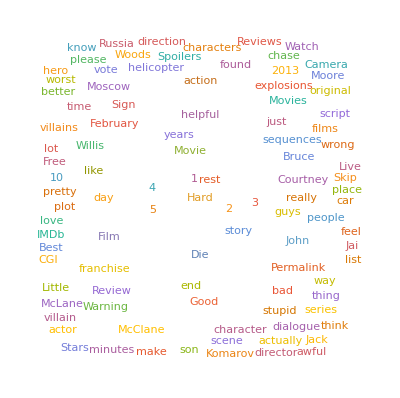

-Graphics-

<|Die→117,Hard→111,movie→87,film→73,action→65,John→61,McClane→53,helpful→50,like→48,good→43,Bruce→42,bad→41,just→39,Willis→34,Good→33,really→32,Day→30,franchise→29,review→28,Sign→28,10→27,found→26,son→26,films→26,Permalink→25,vote→25,time→24,2013→24,car→20,Moscow→19,way→19,February→18,story→17,chase→16,character→16,series→16,2→16,scene→15,Jai→15,movies→15,make→14,Courtney→14,Moore→14,Woods→14,plot→14,5→14,4→14,little→13,love→13,lot→12,people→12,stupid→12,thing→12,guys→12,villains→12,feel→11,helicopter→11,think→11,better→11,Jack→11,Russia→11,day→11,1→11,pretty→10,script→10,Live→10,hero→10,3→10,Komarov→9,actually→9,place→9,Free→9,rest→9,minutes→9,direction→9,worst→9,Stars→9,Spoilers→9,wrong→8,original→8,watch→8,Warning→8,know→8,villain→8,director→8,Skip→8,years→8,sequences→8,IMDb→8,Movies→8,list→7,seen→7,Russian→7,simply→7,quite→7,best→7,makes→7,fan→7,explosions→7,dialogue→7,long→7,got→7,awful→7,actor→7,need→7,end→7,CGI→7,previous→7,characters→7,say→7,Reviews→7,TV→7,Junior→6,McLane→6,titles→6,feels→6,huge→6,fourth→6,effects→6,father→6,goes→6,setting→6,easily→6,Chernobyl→6,building→6,remains→6,guy→6,CIA→6,role→6,comes→6,scenes→6,want→6,die→6,forgettable→6,McClane's→6,point→6,fails→6,lack→6,14→6,7→6,6→6,created→5,Chaganin→5,spark→5,totally→5,31→5,moment→5,gun→5,life→5,terrible→5,lacks→5,try→5,funny→5,moments→5,clear→5,times→5,watching→5,relationship→5,sense→5,Moore's→5,run→5,worse→5,hard→5,excuse→5,John's→5,felt→5,chemistry→5,13→5,hope→5,takes→5,half→5,bullets→5,away→5,Vengeance→5,rating→5,fans→5,mind→5,please→5,death→5,instead→5,old→5,care→5,especially→5,use→5,Oh→5,dumb→5,Gruber→5,else→5,start→5,sidekick→5,weak→5,far→5,instalment→5,fifth→5,said→5,8→5,User→5,Awards→5,Movie→5,video→4,later→4,shooting→4,help→4,audience→4,camera→4,shaky→4,barely→4,Jr.→4,happy→4,Lucy→4,grown→4,scale→4,25→4,talk→4,second→4,problem→4,example→4,one-liners→4,rushed→4,okay→4,name→4,earlier→4,entertainment→4,special→4,tired→4,mess→4,look→4,Alik→4,lines→4,let→4,real→4,Payne→4,Max→4,vacation→4,fact→4,heroes→4,drive→4,waste→4,free→4,course→4,big→4,clever→4,Please→4,15→4,R→4,main→4,works→4,sequence→4,hour→4,right→4,charisma→4,crashes→4,shows→4,stop→4,opening→4,clearly→4,writer→4,absurd→4,screen→4,9→4,past→4,Celebs→4,News→4,ago→3,months→3,External→3,file→3,straight→3,remember→3,energy→3,appears→3,generic→3,involved→3,heart→3,machine→3,minute→3,learn→3,street→3,12→3,certainly→3,returns→3,etc→3,rubbish→3,2020→3,close→3,%→3,Camera→3,Shaky→3,37→3,gone→3,military→3,guns→3,Hards→3,positive→3,ending→3,five→3,took→3,heard→3,fit→3,play→3,asked→3,Hans→3,fine→3,gave→3,sure→3,confusing→3,threat→3,nice→3,tried→3,material→3,PG-13→3,viewer→3,work→3,plays→3,pass→3,editing→3,art→3,piece→3,left→3,open→3,17→3,route→3,Koch→3,Sebastian→3,offers→3,making→3,basics→3,news→3,bang→3,4.0→3,HARD→3,DIE→3,attempt→3,played→3,third→3,witty→3,hardly→3,gets→3,sound→3,monotonous→3,despite→3,round→3,police→3,supposed→3,capital→3,destruction→3,drawn→3,latter→3,tries→3,sequel→3,boring→3,loud→3,pointless→3,money→3,cast→3,simple→3,home→3,fly→3,surprise→3,tell→3,plant→3,nuclear→3,grade→3,weapons→3,shot→3,men→3,Jr→3,career→3,violence→3,executed→3,cars→3,forced→3,going→3,virtually→3,country→3,dissident→3,trying→3,usual→3,latest→3,20→3,grow→3,jokes→3,focus→3,sucks→3,great→3,ass→3,stuck→3,Russians→3,Rambo→3,man→3,Wills→3,killed→3,falling→3,believe→3,McTiernan→3,bring→3,final→3,6th→3,music→3,turns→3,exciting→3,massive→3,pleasure→3,enjoyed→3,sensational→3,97→3,evil→3,none→3,cut→3,signs→3,vulnerable→3,missed→3,eyes→3,doubt→3,given→3,favorite→3,save→3,line→3,worthy→3,writing→3,Review→3,v→3,States→3,Central→3,Festival→3,Film→3,Best→3,Watch→3,Shows→3,Popular→3,Top→3,access→2,App→2,Action→2,lists→2,Related→2,Photo→2,Plot→2,Credits→2,Sites→2,Metacritic→2,Ratings→2,FAQ→2,inside→2,vehicle→2,stashed→2,company→2,pistol→2,struggling→2,Winstead→2,daughter→2,Everybody→2,utter→2,scenarist→2,Sadly→2,Detective→2,entirely→2,saw→2,Worst→2,dull→2,face→2,bound→2,personal→2,value→2,set→2,terms→2,urgency→2,performance→2,laziness→2,technically→2,26→2,regard→2,Harder→2,hear→2,it'll→2,DVD→2,unless→2,error→2,factual→2,power→2,looks→2,stolen→2,rounds→2,courthouse→2,border→2,km→2,able→2,driver→2,taxi→2,target→2,American→2,errors→2,entertaining→2,ridiculous→2,named→2,jail→2,flat→2,pulls→2,fire→2,August→2,kill→2,Sam→2,sorry→2,says→2,Reacher→2,Mclane→2,random→2,Courtney's→2,Snigir→2,Kolesnikov→2,Sergey→2,follow→2,act→2,shoot→2,construction→2,ten→2,poor→2,biggest→2,cinema→2,ruined→2,ended→2,buy→2,twice→2,jump→2,died→2,fell→2,pulled→2,advanced→2,Bad→2,21→2,note→2,cliché→2,came→2,estranged→2,family→2,unlike→2,chaos→2,international→2,wanted→2,sadly→2,hate→2,walk→2,oh→2,Bourne→2,brat→2,spoiled→2,summary→2,Yes→2,hours→2,couple→2,gonna→2,alright→2,longer→2,Fox→2,feeling→2,Let→2,23→2,generally→2,properly→2,poorly→2,humour→2,coming→2,stunts→2,low→2,come→2,annoying→2,lead→2,apart→2,sounded→2,looked→2,chaotic→2,serves→2,locations→2,choice→2,disappointing→2,evident→2,audiences→2,large→2,distance→2,chance→2,brutal→2,meant→2,gritty→2,reeks→2,stunt→2,honest→2,pure→2,'90s→2,'80s→2,God→2,early→2,whatever→2,plans→2,kind→2,idea→2,brought→2,charm→2,voice→2,effort→2,guess→2,written→2,actors→2,comparison→2,trilogy→2,30→2,possibly→2,entry→2,page→2,Bukvic→2,Rasha→2,hand→2,inane→2,lamenting→2,father-son→2,context→2,humorous→2,wise→2,Ironically→2,quickly→2,tiresome→2,plus→2,pacing→2,things→2,pay→2,firing→2,order→2,law→2,explain→2,uranium→2,using→2,yes→2,Americans→2,century→2,21st→2,worth→2,change→2,manage→2,imprisoned→2,matter→2,thinks→2,proof→2,filmography→2,former→2,directing→2,loved→2,attitude→2,mean→2,age→2,reason→2,80s→2,predecessor→2,Indeed→2,chapter→2,entire→2,resemble→2,fun→2,figures→2,addition→2,lame→2,uninteresting→2,member→2,job→2,bit→2,exception→2,result→2,tension→2,went→2,pain→2,thought→2,god→2,person→2,complex→2,happen→2,crap→2,deal→2,based→2,knew→2,standards→2,due→2,installment→2,neither→2,matters→2,apparently→2,happens→2,Lucky→2,radiation→2,science→2,falls→2,thrown→2,blown→2,small→2,tap→2,fast→2,giving→2,knife→2,getting→2,operative→2,working→2,finds→2,reconnect→2,Hollywood→2,impact→2,avoid→2,sequels→2,children→2,hair→2,anymore→2,laughing→2,hurt→2,painful→2,worked→2,understand→2,horrible→2,fighting→2,army→2,forever→2,spoilers→2,destroy→2,deserve→2,sunset→2,goods→2,Harlin→2,Renny→2,Michael→2,cinematography→2,load→2,hold→2,throughout→2,destructive→2,sort→2,guilty→2,film's→2,heavily→2,climax→2,motion→2,slow→2,heavy→2,puts→2,crash→2,subtlety→2,running→2,length→2,shortest→2,memorable→2,menacing→2,hell→2,short→2,development→2,killing→2,major→2,damage→2,mass→2,step→2,seriously→2,blame→2,turned→2,wisecracks→2,son's→2,yay→2,ki→2,R-rating→2,IV→2,Rocky→2,mentioned→2,bet→2,weaker→2,ends→2,saga→2,beloved→2,Rating→2,akci→2,Opět→2,Smrtonosná→2,Español→2,Français→2,United→2,supported→2,Keywords→2,Help→2,York→2,New→2,Comic-Con→2,Winners→2,Picture→2,2022→2,Events→2,Trailers→2,Spotlight→2,India→2,Showtimes→2,Office→2,Box→2,Genre→2,Browse→2,250→2,Release→2,Inc→1,IMDb.com→1,1990-2022→1,©→1,Amazon→1,Ads→1,Interest-Based→1,Policy→1,Privacy→1,Use→1,Conditions→1,Jobs→1,Advertising→1,Room→1,Press→1,Developer→1,Mojo→1,IMDbPro→1,Index→1,Site→1,Viewed→1,Recently→1,history→1,Clear→1,Share→1,related→1,11→1,Apr→1,46→1,Thing→1,29→1,ST→1,Jun→1,01→1,1982-2020→1,Franchises→1,List→1,Rankings→1,users→1,Lists→1,Create→1,Explore→1,Items→1,Videos→1,Gallery→1,Video→1,Soundtracks→1,Connections→1,Versions→1,Alternate→1,Quotes→1,Crazy→1,Goofs→1,Trivia→1,Know→1,Guide→1,Parents→1,Synopsis→1,Summary→1,Taglines→1,Storyline→1,Specs→1,Technical→1,Production→1,Filming→1,Company→1,Official→1,Dates→1,Crew→1,Cast→1,Details→1,Opinion→1,Load→1,occured→1,ultimately→1,finished→1,complaint→1,bland→1,relief→1,comic→1,highly→1,magic→1,seemingly→1,size→1,classic→1,2019→1,Floated2→1,Bottom→1,above-mentioned→1,blowing→1,struggle→1,filmmakers→1,surprising→1,surprises→1,attached→1,Swordfish→1,fireball→1,qualifies→1,intended→1,miss→1,angle→1,precipitous→1,backwards→1,tilts→1,bay→1,cargo→1,drives→1,cranks→1,stalwart→1,hiding→1,office→1,riddle→1,chopper→1,commandeers→1,aboard→1,scrambles→1,scrapes→1,surviving→1,dodge→1,somewhat→1,reconcile→1,Irons→1,Jeremy→1,Rickman→1,Alan→1,debonair→1,deadly→1,ruins→1,sinister→1,grab→1,betray→1,Komarovs→1,Eventually→1,mysterious→1,interference→1,tags→1,elude→1,desperately→1,orchestrated→1,spectacularly→1,ensues→1,automotive→1,demolition-derby→1,neck→1,Junior's→1,breathing→1,Meantime→1,confronts→1,raid→1,prison→1,shoots→1,younger→1,hates→1,Taken→1,led→1,gunsels→1,gang→1,dispatches→1,dispose→1,Agent→1,specifically→1,Minister→1,Defense→1,position→1,campaigning→1,wicked→1,incriminating→1,claims→1,elusive→1,sons→1,camaraderie→1,advance→1,teach→1,dodging→1,opposition→1,blasting→1,mumble→1,reminisce→1,quiet→1,associate→1,reprising→1,Aside→1,Elizabeth→1,Mary→1,obligatory→1,flies→1,Naturally→1,Agency→1,Intelligence→1,spook→1,elder→1,learns→1,range→1,NYPD→1,targets→1,indestructible→1,radiates→1,fame→1,Avatar→1,Worthington→1,resembles→1,unknown→1,largely→1,cross-fire→1,caught→1,partner→1,expendable→1,Hauser→1,Cole→1,recognize→1,Basically→1,assist→1,derring→1,feats→1,performs→1,motto→1,intervals→1,Consequently→1,thwart→1,form→1,Lieutenant→1,Expendables→1,wants→1,Ultimately→1,chess→1,playing→1,bides→1,Unknown→1,bearded→1,wealthy→1,galore→1,influence→1,politician→1,high-ranking→1,clean-shaven→1,Souls→1,Cold→1,allies→1,political→1,confined→1,Christmas→1,occur→1,Unlike→1,tense→1,thriller→1,raw-edged→1,inserted→1,Century→1,20th→1,strong→1,generates→1,competition→1,distinguish→1,Spartan→1,larger-than-life→1,boasts→1,epics→1,taken→1,actioneer→1,98-minute→1,formulaic→1,fast-paced→1,distinction→1,dubious→1,acquired→1,remembered→1,zardoz-13→1,18→1,arf→1,Vienna→1,memories→1,teenage→1,fond→1,erases→1,Kane→1,Citizen→1,Commando→1,firefights→1,chases→1,95→1,98→1,Scene→1,Exciting→1,Edgy→1,dad→1,pointing→1,responding→1,million→1,city→1,into→1,bumping→1,DH4→1,losing→1,Long's→1,DH3→1,Zeus→1,DH2→1,numerous→1,DH1→1,characteristic→1,defining→1,meter→1,parking→1,McLane's→1,begin→1,helm→1,poster→1,reviews→1,stellar→1,read→1,paying→1,indifference→1,total→1,feelings→1,pipeline→1,DH→1,poorest→1,diminishing→1,perfect→1,Tin-3→1,Tin→1,call→1,project→1,smothered→1,blockbuster→1,board→1,lacking→1,shortcomings→1,consistent→1,connection→1,front→1,happened→1,delivering→1,surprised→1,thrilled→1,nonsense→1,overblown→1,OK→1,impressive→1,pieces→1,buck→1,feeds→1,unfortunately→1,charismatic→1,presence→1,arms→1,matched→1,twinkle→1,approaching→1,sold→1,convinced→1,compare→1,caring→1,tensions→1,specific→1,raise→1,anyway→1,smother→1,effectively→1,Clay→1,Bill→1,nods→1,slightest→1,flow→1,continues→1,accommodating→1,intelligence→1,insult→1,middle→1,bump→1,basic→1,pitch→1,beyond→1,case→1,tenuous→1,mould→1,traditional→1,writers→1,excited→1,reasons→1,seat→1,kicking→1,kid→1,coach→1,flew→1,official→1,lag→1,Jet→1,sighing→1,fed→1,criticism→1,self-contained→1,promote→1,BBC1's→1,appearing→1,online→1,clip→1,moo→1,bob→1,Lacking→1,257→1,187→1,fight→1,problems→1,belongs→1,America→1,stayed→1,aliens→1,whirlwind→1,Jones→1,Indiana→1,twisted→1,Europe→1,Oceans→1,kids→1,1988→1,Jake→1,mentions→1,benefited→1,moved→1,rank→1,noise→1,background→1,edition→1,extended→1,Maybe→1,junk→1,probably→1,loyal→1,gogeestar→1,Forget→1,44→1,memory→1,garbage→1,noticeable→1,content→1,pinch→1,intuition→1,smarts→1,provoked→1,non-aggressive→1,crashing→1,rotor→1,tail→1,magical→1,helicopters→1,swim→1,happily→1,radiated→1,water→1,Rain→1,metal→1,blower→1,leaf→1,dispersed→1,Dozens→1,Pripyat→1,1000→1,Car→1,interfere→1,downtown→1,buildings→1,countries→1,figure→1,bandits→1,Chechen→1,Canadian→1,trunk→1,Ukraine→1,protagonist→1,anti-tank→1,twin→1,3000→1,retarded→1,drag→1,artificial→1,stares→1,violin→1,Especially→1,constantly→1,drama→1,issue→1,jumping→1,Okay→1,wandering→1,reunions→1,organize→1,perpetrators→1,occurs→1,firefight→1,casual→1,checks→1,ID→1,corner→1,policemen→1,normally→1,state→1,NATO→1,nearest→1,700→1,2000's→1,drone→1,systems→1,air→1,anti-→1,radars→1,1940's→1,travel→1,fiction→1,instant→1,flying→1,Drone→1,UAV→1,Dozen→1,youthful→1,emulate→1,friendship→1,ode→1,embarrassing→1,starts→1,lobotomy→1,received→1,approved→1,directed→1,populated→1,world→1,conclusion→1,continued→1,reaction→1,initial→1,usually→1,geography→1,logic→1,idiotic→1,downright→1,loads→1,inc-10→1,compelling→1,vehicles→1,wreck→1,gall→1,astonishment→1,staring→1,amount→1,Yuliya→1,Irina→1,woman→1,young→1,alluring→1,files→1,sent→1,agent→1,trouble→1,rescue→1,cop→1,basically→1,24→1,tavm→1,ok→1,humor→1,gunfights→1,decent→1,referenced→1,practical→1,green→1,relied→1,positives→1,dumpster→1,complete→1,letdown→1,2021→1,28→1,tylerrosin→1,103→1,66→1,Skyfall→1,managed→1,007→1,Mendes→1,Damme→1,Van→1,treated→1,expectations→1,acting→1,PG→1,forget→1,descent→1,cardboard→1,bad-guys→1,brain-dead→1,100→1,totals→1,Like→1,craving→1,satisfy→1,add→1,suppose→1,Courteny→1,describe→1,Thats→1,krycek19→1,Annoying→1,302→1,243→1,suggest→1,hard-core→1,Bring→1,begging→1,year→1,starred→1,messes→1,12A→1,'s→1,Aka→1,Hard's→1,complaining→1,changed→1,cgi→1,movie_star349→1,tarnishing→1,allow→1,ego→1,dude→1,bald→1,invulnerable→1,morphed→1,physically→1,flawed→1,paycheque→1,juicy→1,crack→1,bullet→1,piss→1,greatest→1,incredible→1,March→1,Chris_Mac_25→1,Rubbish→1,afterwards→1,judicious→1,filming→1,presumption→1,exaggerated→1,best-executed→1,American-style→1,avenues→1,maddening→1,etc.→1,situation→1,regardless→1,unharmed→1,Afghanistan→1,invade→1,clichés→1,evoke→1,emotion→1,danger→1,game→1,noisy→1,illogical→1,space→1,tastes→1,visual→1,level→1,technical→1,male→1,path→1,Yulia→1,superficial→1,limit→1,Luknár→1,Roman→1,believable→1,establish→1,cane→1,notable→1,outstanding→1,voices→1,bodies→1,invited→1,personality→1,faces→1,leaves→1,moral→1,psychological→1,sacrificing→1,dialogues→1,foundation→1,solid→1,cohesive→1,absence→1,conducive→1,environments→1,allows→1,oligarch→1,mafia→1,arrest→1,penalty→1,gunshots→1,throws→1,starting→1,bets→1,incompetence→1,interesting→1,merit→1,consolidate→1,helped→1,glory→1,April→1,filipemanuelneto→1,Kill→1,273→1,213→1,un-needed→1,unwanted→1,moves→1,houses→1,directors→1,Just→1,netflix→1,download→1,cinemas→1,feature→1,species→1,remaining→1,PLEASE→1,Films→1,STOP→1,ins→1,zoom→1,rapid→1,blurry→1,35→1,16→1,heil_cf2→1,49→1,Yippee→1,Yep→1,thoughts→1,finally→1,exact→1,dies→1,scratch→1,tall→1,MeClane→1,fall→1,stage→1,Hercules→1,Xena→1,Aries→1,Smith→1,Kevin→1,bandage→1,gut→1,steel→1,bar→1,235→1,Uranium→1,bomb→1,refined→1,tons→1,decades→1,abandon→1,conveniently→1,governments→1,Soviet→1,information→1,mission→1,three-year→1,exactly→1,hands→1,destroyed→1,kajillion→1,blazing→1,cops→1,Apparently→1,search→1,idiot→1,Poor→1,performances→1,Wooden→1,damn→1,tickets→1,wonder→1,Minerva_Meybridge→1,653→1,538→1,stay→1,sh*t→1,dead→1,brain→1,dying→1,carries→1,Bukvić→1,Radivoje→1,speak→1,pulling→1,introduced→1,father-daughter→1,focused→1,primarily→1,lose→1,carried→1,threats→1,terrorist→1,numb→1,finish→1,endless→1,stakes→1,smallest→1,ironically→1,logically→1,nation→1,NYC→1,airport→1,larger→1,promised→1,selling→1,notoriously→1,join→1,Omen→1,remake→1,Look→1,soon→1,Q→1,neyoless→1,bearer→1,604→1,512→1,dear→1,football→1,tree→1,eventually→1,reading→1,choose→1,environment→1,tested→1,outside→1,trivial→1,sounds→1,USA→1,bangs→1,production→1,post→1,sandwiched→1,Jason→1,pretending→1,discern→1,parodies→1,factor→1,Super-villain→1,side-kick→1,concise→1,warn→1,andrewsmith1-609-479980→1,220→1,191→1,bigger→1,smaller→1,Mctiernan→1,shaky-cam→1,disturbed→1,enjoyable→1,twist→1,possible→1,structure→1,explore→1,ans→1,dialog→1,trust→1,idiots→1,A-Team→1,saying→1,michaelberneman→1,Great→1,Cox→1,Bethany→1,3/10→1,seeing→1,string→1,implausibility→1,increasing→1,drags→1,crosses→1,double→1,sagged→1,hollow→1,emotionally→1,Spy→1,Soldier→1,Tailor→1,Tinker→1,criticised→1,understanding→1,timed→1,out-of-place→1,rambling→1,unsubtle→1,wannabe-big→1,unscathed→1,dangerous-looking→1,peril→1,excitement→1,momentum→1,slick→1,near→1,particularly→1,suffers→1,shadow→1,motivation→1,underdeveloped→1,non-entity→1,dynamic→1,likable→1,saddled→1,iconic→1,commanding→1,sidelined→1,disadvantaged→1,world-weary→1,maybe→1,cohesion→1,degrees→1,pedestrian→1,lazy→1,sensitive→1,epilepsy→1,suffering→1,ideal→1,nature→1,appropriately→1,inconsistent→1,photography→1,absolute→1,tad→1,overall→1,mood→1,atmosphere→1,scored→1,qualities→1,redeeming→1,prize→1,win→1,contender→1,award→1,MoVie→1,Scary→1,Earth→1,consider→1,disappointment→1,genre→1,greats→1,all-time→1,September→1,TheLittleSongbird→1,162→1,117→1,sake→1,time's→1,beater→1,wife→1,hang→1,co.→1,LFODH→1,execrable→1,handle→1,inability→1,director's→1,true→1,backlash→1,suspect→1,mediocre→1,saved→1,R.→1,rated→1,decided→1,makers→1,portrayal→1,opposite→1,stiff→1,lifeless→1,root→1,saving→1,impedes→1,anger→1,outbursts→1,legendary→1,hero's→1,Bauer→1,beefed→1,plausible→1,timeless→1,intensity→1,raw→1,Asia→1,Southeast→1,regime→1,technology→1,current→1,modern→1,relic→1,adapt→1,continue→1,apparent→1,unfunny→1,screenplay→1,homages→1,words→1,bravado→1,enemies→1,kills→1,insights→1,deep→1,morality→1,instances→1,heartwarming→1,hilt→1,date→1,Bay-esque→1,scream→1,hijinks→1,ostentatious→1,known→1,trappings→1,commendable→1,aspect→1,willing→1,craftsmanship→1,MTV→1,quick-style→1,integrity→1,class→1,thought-provoking→1,Sure→1,johnnymacbest→1,desired→1,kept→1,whimper→1,CGI-fuelled→1,en→1,wasted→1,visuals→1,purely→1,half-decent→1,explosive→1,routine→1,mind-numblingly→1,stumbles→1,meanders→1,SAND→1,BLOOD→1,SPARTACUS→1,Varro→1,displays→1,one-dimensional→1,sleep→1,moviegoers→1,send→1,guaranteed→1,sleepwalks→1,whatsoever→1,turkey→1,realises→1,anybody's→1,employ→1,currently→1,A-TEAM→1,rubbishy→1,equally→1,handled→1,appalling→1,screw→1,manages→1,shots→1,PAYNE→1,MAX→1,door→1,laid→1,masterpiece→1,followed→1,DAY→1,GOOD→1,Inevitably→1,slap→1,Willis-starring→1,successful→1,moderately→1,release→1,slated→1,June→1,Leofwine_draca→1,bringing→1,Pitiful→1,260→1,195→1,mistake→1,unfortunate→1,landing→1,penchant→1,knell→1,baton→1,passing→1,new→1,lamentable→1,appreciated→1,dancer→1,used→1,talks→1,nemesis→1,cake→1,horrid→1,suit→1,protective→1,stepping→1,topic→1,expected→1,respect→1,nary→1,consisting→1,repetitive→1,frustratingly→1,engaging→1,cracks→1,passes→1,laughable→1,slo-mo→1,incredulous→1,grows→1,the-top→1,over→1,thrills→1,genuine→1,compensate→1,over-used→1,weaponry→1,cranked→1,perpetually→1,excite→1,unimaginatively→1,staged→1,fired→1,Shots→1,bore→1,pace→1,frenetic→1,telling→1,details→1,attention→1,expediency→1,common→1,shred→1,ignore→1,escapist→1,high-rise→1,responds→1,authority→1,infrastructure→1,city's→1,decimates→1,highway→1,nonchalant→1,busy→1,agency→1,sign→1,following→1,credibility→1,strains→1,premise→1,realise→1,daft→1,build→1,site→1,plan→1,nefarious→1,Russian's→1,nasty→1,foiling→1,institution→1,archaic→1,nationalities→1,stereotypes→1,cue→1,respectively→1,location→1,convince→1,lost→1,havoc→1,wreak→1,transport→1,decides→1,turf→1,detective→1,City→1,putting→1,Impossible→1,Mission→1,consistency→1,foolish→1,blandness→1,exercise→1,mediocrity→1,rising→1,capable→1,suggests→1,Little→1,scripting→1,combination→1,toxic→1,severely→1,90s→1,wisecracking→1,unflappable→1,squint→1,trademark→1,mention→1,kick→1,weapon→1,carry→1,57→1,told→1,Truth→1,passable→1,firmly→1,sensibilities→1,new-age→1,heroics→1,old-school→1,formula→1,winning→1,banked→1,immediate→1,erroneously-titled→1,plain→1,ground→1,burn→1,movie-making→1,important→1,restarting→1,successfully→1,Six→1,Truly→1,hearts→1,moviexclusive→1,days→1,461→1,357→1,intention→1,overuse→1,drain→1,fallen→1,anticipated→1,absolutely→1,messy→1,sell→1,appeal→1,fantastic→1,relatability→1,tone→1,resembled→1,bear→1,regular→1,happening→1,dumbest→1,whereas→1,attempts→1,begins→1,issues→1,travels→1,BOY→1,turn→1,high→1,invincible→1,superhero→1,4th→1,connect→1,phenomenal→1,Jackson→1,mainly→1,3rd→1,illbebackreviews→1,Franchise→1,140→1,121→1,yelling→1,keeps→1,joke→1,film-fans→1,disappointed→1,bystanders→1,innocent→1,corpses→1,littered→1,smoking→1,leave→1,glow→1,Dad→1,calls→1,neglect→1,forgives→1,None→1,boot→1,arsenal→1,steal→1,suburb→1,mayhem→1,arrival→1,Bruce's→1,protection→1,stubble→1,defunct→1,rushes→1,iPad→1,Domestos→1,squirt→1,quick→1,eradicated→1,pooling→1,twists→1,baddies→1,Stupid→1,realistic→1,window→1,beaten→1,grubbier→1,singlet→1,white→1,regulation→1,limp-free→1,unmarked→1,giggling→1,distracting→1,armed→1,dozen→1,overwhelm→1,break→1,dancing→1,emote→1,carrot→1,eat→1,slows→1,suddenly→1,mindless→1,hundred→1,slaughtered→1,captured→1,pair→1,Apache→1,ones→1,dodged→1,steer→1,plenty→1,dog→1,ball→1,tennis→1,throwing→1,velocity→1,launched→1,rocket→1,RPG→1,walls→1,bulldoze→1,chasing→1,armoured→1,butter→1,jams→1,traffic→1,dense→1,roars→1,van→1,transit→1,rush→1,derbying→1,demolition→1,meal→1,cream→1,ice→1,considered→1,follows→1,nose→1,thumbing→1,safety→1,pesky→1,joins→1,vague→1,smuggle→1,bid→1,errant→1,tracks→1,McClean→1,spare→1,room→1,nutshell→1,Thunderbirds→1,episode→1,emotional→1,unbelievable→1,cartoonishly→1,unbearably→1,Loud→1,offering→1,nearly→1,folks→1,BJBatimdb→1,Cry→1,120→1,101→1,Thanks→1,scumbags→1,retire→1,plague→1,1/10→1,Score→1,morons→1,brainless→1,animated→1,bleed→1,fake→1,glass→1,exist→1,collection→1,hill→1,disaster→1,fucking→1,opinion→1,grove→1,sidekicks→1,critics→1,bashed→1,80's→1,different→1,dialed→1,Stallone→1,II→1,Blood→1,filmed→1,digitally→1,unlikable→1,terrorists→1,team→1,dammit→1,bored→1,blow→1,business→1,contain→1,2018→1,ivo-cobra8→1,612→1,534→1,Shame→1,British→1,respected→1,horse→1,ride→1,deliver→1,strongly→1,school→1,delivers→1,screenwriter→1,hire→1,Wiseman→1,Len→1,brainer→1,according→1,themes→1,Kamen's→1,incorporating→1,stuff→1,knows→1,Beltrami→1,Marco→1,score→1,riveting→1,Sela→1,Jonathan→1,competent→1,wait→1,boy→1,hoo→1,F-35→1,Terminator→1,essentially→1,Pity→1,intense→1,streets→1,stunt-filled→1,beginning→1,relies→1,excruciatingly→1,cuts→1,smash→1,directs→1,added→1,could've→1,Imagine→1,complained→1,released→1,runs→1,humanity→1,dealing→1,Weapons→1,deeds→1,dastardly→1,intelligent→1,smirking→1,Brothers→1,Stuart→1,Colonel→1,Gabriel→1,Thomas→1,likes→1,primary→1,merciless→1,glimpses→1,certain→1,filling→1,pop→1,wherever→1,qualms→1,vulnerability→1,attacking→1,thugs→1,vehicular→1,causes→1,immediately→1,ahead→1,calculative→1,cool→1,adversaries→1,wounded→1,reluctant→1,stops→1,Joe→1,everyday→1,human→1,likability→1,essence→1,near-crap→1,fault→1,cynicism→1,weathered→1,dishes→1,bless→1,supercop→1,wise-cracking→1,reduced→1,visible→1,trait→1,key→1,shaped→1,thrust→1,inexplicably→1,relegated→1,treatment→1,horrendous→1,mine→1,Yippie→1,famous→1,return→1,Robin→1,Batman→1,Control→1,Cruise→1,Speed→1,Peace→1,Quest→1,Superman→1,V→1,sentence→1,incoherent→1,characterization→1,thanks→1,falters→1,dud→1,sad→1,heartbroken→1,dvc5159→1,earth→1,Star→1,Filter→1,Reviewer→1,Prolific→1,Votes→1,Total→1,Date→1,Featured→1,Sort→1,Hide→1,607→1,title→1,México→1,España→1,Brasil→1,Português→1,Italia→1,Italiano→1,भारत→1,हिंदी→1,Deutschland→1,Deutsch→1,France→1,Canada→1,Partially→1,English→1,Fully→1,EN→1,Watchlist→1,Search→1,Advanced→1,Companies→1,Episodes→1,Titles→1,Professionals→1,Industry→1,Polls→1,Zone→1,Contributor→1,Center→1,Community→1,Celebrity→1,Today→1,Born→1,Int'l→1,Toronto→1,Sundance→1,Diego→1,San→1,STARmeter→1,Emmys→1,Oscars→1,Podcasts→1,Picks→1,Originals→1,Latest→1,Streaming→1,Tickets→1,Calendar→1,Menu→1|>

```mathematica
text1 =plaintext1;
plaintext1=Import["https://www.imdb.com/title/tt1606378/reviews?ref_=tt_urv"<>ToString@45,"Plaintext"];

Snippet["https://www.imdb.com/title/tt1606378/reviews?ref_=tt_urv"] 
WordCloud[DeleteStopwords [text1]]

WordCloud[Classify["Sentiment",text1]
]
WordCounts[DeleteStopwords [text1]]
```

https://www.imdb.com/title/tt0381849/reviews?sort=curated&dir=desc&ratingFilter=

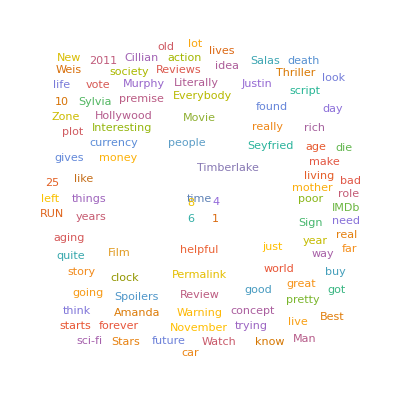

-Graphics-

<|time→163,film→59,movie→54,helpful→50,Timberlake→48,like→42,people→37,just→36,Time→34,rich→33,world→32,found→31,live→30,Sign→28,clock→27,review→26,10→26,Permalink→25,vote→25,Justin→25,really→22,poor→22,good→22,idea→22,25→21,money→19,Seyfried→19,years→19,life→19,Amanda→18,things→18,year→18,make→16,die→15,currency→15,man→14,left→14,Salas→14,day→14,way→14,1→14,lot→13,action→13,future→13,story→12,plot→12,Murphy→12,age→12,2011→12,know→11,Spoilers→11,Weis→10,forever→10,think→10,Cillian→10,premise→10,got→10,Sylvia→10,Warning→10,going→10,6→10,script→9,gives→9,role→9,new→9,look→9,buy→9,car→9,pretty→9,trying→9,great→9,8→9,4→9,Stars→9,Reviews→9,thriller→8,real→8,starts→8,old→8,quite→8,run→8,living→8,watch→8,Hollywood→8,literally→8,takes→8,zone→8,need→8,death→8,thought→8,concept→8,mother→8,lives→8,society→8,aging→8,November→8,far→8,IMDb→8,TV→8,list→7,away→7,bad→7,worth→7,wealth→7,Great→7,acting→7,better→7,interesting→7,point→7,little→7,stupid→7,everybody→7,sci-fi→7,work→7,2013→7,genetically→6,spend→6,costs→6,end→6,love→6,job→6,best→6,chemistry→6,character→6,executed→6,dies→6,given→6,Bonnie→6,guy→6,enjoyed→6,sort→6,played→6,24→6,scenes→6,steal→6,cast→6,pay→6,Will's→6,want→6,believe→6,try→6,Hamilton→6,Wilde→6,ghetto→6,earn→6,created→5,titles→5,%→5,makes→5,Clyde→5,engineered→5,waste→5,minutes→5,gets→5,plays→5,actor→5,sense→5,characters→5,turn→5,stop→5,futuristic→5,Silvia→5,times→5,person→5,use→5,Clock→5,set→5,stars→5,young→5,2012→5,throughout→5,ticking→5,TIME→5,enjoyable→5,11→5,girl→5,Leon→5,fight→5,lead→5,crash→5,fact→5,wrist→5,arm→5,bank→5,Henry→5,Olivia→5,science→5,7→5,5→5,User→5,Awards→5,Movies→5,ago→4,hours→4,suddenly→4,ideas→4,message→4,stolen→4,reach→4,daughter→4,scene→4,likely→4,main→4,getting→4,original→4,longer→4,felt→4,written→4,say→4,works→4,chase→4,long→4,unless→4,come→4,taken→4,cross→4,zones→4,strong→4,early→4,decent→4,watching→4,happen→4,seen→4,actors→4,reason→4,bar→4,friend→4,constantly→4,forearm→4,means→4,Andrew→4,right→4,wrong→4,runs→4,holes→4,hour→4,hand→4,believable→4,high→4,security→4,touch→4,zero→4,9→4,3→4,2→4,Celebs→4,Best→4,News→4,External→3,tries→3,born→3,performance→3,banks→3,Scene→3,month→3,poorly→3,Seyfield→3,shame→3,effects→3,15→3,interested→3,fairly→3,reviews→3,dramatic→3,Rich→3,asleep→3,hands→3,plenty→3,thrilling→3,dystopian→3,thing→3,deal→3,poker→3,uses→3,goes→3,area→3,using→3,seeing→3,hundred→3,class→3,People→3,definitely→3,coming→3,looking→3,body→3,cash→3,cool→3,instead→3,bored→3,game→3,fully→3,tale→3,revenge→3,bus→3,begins→3,watched→3,course→3,short→3,fall→3,disappointing→3,type→3,clocks→3,seconds→3,spent→3,question→3,Raymond→3,Timekeeper→3,running→3,writer→3,clever→3,Just→3,word→3,social→3,system→3,children→3,100→3,26→3,Timberlake's→3,Hood→3,Robin→3,turns→3,line→3,ages→3,genre→3,fiction→3,able→3,classes→3,start→3,recommend→3,bit→3,nice→3,Kartheiser→3,Vincent→3,30→3,unique→3,stranger→3,cost→3,save→3,hoping→3,50→3,else→3,factory→3,population→3,keeps→3,enjoy→3,talent→3,due→3,hero→3,central→3,director→3,potential→3,actually→3,simple→3,October→3,viewer→3,Greenwich→3,days→3,28→3,months→3,looked→3,playing→3,buying→3,tell→3,father→3,Literally→3,dying→3,easy→3,rob→3,place→3,play→3,robbing→3,older→3,tired→3,Rachel→3,Everybody→3,stopped→3,Review→3,Festival→3,New→3,Watch→3,Shows→3,Movie→3,Popular→3,Top→3,access→2,App→2,lists→2,Related→2,Photo→2,Plot→2,Credits→2,Sites→2,Metacritic→2,Ratings→2,FAQ→2,scifi→2,page→2,winning→2,19→2,Timekeepers→2,Minutemen→2,gone→2,Gattica→2,past→2,attack→2,heart→2,wasting→2,Syndrome→2,Stockholm→2,create→2,skin→2,hope→2,despite→2,economy→2,solve→2,predictable→2,making→2,based→2,instantly→2,directed→2,frame→2,problem→2,touched→2,resolution→2,sector→2,Gattaca→2,wins→2,win→2,expectancy→2,faces→2,deserves→2,intelligence→2,moments→2,air→2,loses→2,reality→2,delivering→2,smart→2,allegory→2,contrast→2,April→2,highly→2,strongly→2,typical→2,understanding→2,Firstly→2,political→2,loved→2,responses→2,negative→2,phones→2,devices→2,design→2,stiff→2,convincing→2,lacks→2,supposed→2,commentary→2,features→2,cut→2,Run→2,Logan's→2,thinking→2,computer→2,alive→2,stay→2,struggling→2,Overall→2,final→2,amount→2,fair→2,catch→2,Keeper→2,impresses→2,Hearst→2,Patty→2,expense→2,endless→2,dark→2,unusual→2,unexpected→2,wealthiest→2,Keepers→2,late→2,share→2,escape→2,attention→2,drink→2,avoid→2,provoking→2,probably→2,cars→2,depicted→2,struggle→2,Phillipe→2,warfare→2,Mom→2,wealthy→2,fail→2,wisely→2,spot→2,ride→2,credit→2,today→2,depth→2,gave→2,five→2,twenty→2,depends→2,gold→2,boring→2,expected→2,giving→2,taking→2,kidnaps→2,meets→2,awesome→2,emotions→2,Siegfried→2,sounded→2,dead→2,likable→2,beautiful→2,paid→2,coffee→2,digital→2,Surprisingly→2,tension→2,movies→2,movement→2,Occupy→2,Pettyfer→2,Alex→2,entertaining→2,wanted→2,deep→2,March→2,opposite→2,developed→2,close→2,stealing→2,accused→2,extremely→2,centuries→2,Poorly→2,18→2,clearly→2,picking→2,spending→2,Nichol→2,commodity→2,intriguing→2,sure→2,wonder→2,2018→2,disbelief→2,Pretty→2,timekeeper→2,spoiled→2,suicidal→2,huge→2,stops→2,countdown→2,borrowed→2,decided→2,fine→2,distracted→2,straight→2,impressed→2,danger→2,piece→2,wants→2,possible→2,chance→2,except→2,13→2,romance→2,wish→2,treasure→2,risks→2,multiple→2,possibility→2,liked→2,richest→2,parts→2,call→2,follow→2,different→2,etc→2,drama→2,overall→2,name→2,familiar→2,glad→2,saw→2,September→2,production→2,appeal→2,professional→2,leading→2,roles→2,supporting→2,challenge→2,allowing→2,advertised→2,century→2,Galecki→2,Johnny→2,Borel→2,drinking→2,Dayton→2,worker→2,desperate→2,reminder→2,constant→2,mediocre→2,rating→2,help→2,film's→2,screen→2,hard→2,wooden→2,worst→2,comes→2,excellent→2,Niccol→2,films→2,recent→2,suspense→2,lots→2,thanks→2,sell→2,twist→2,depiction→2,bears→2,2015→2,execution→2,mind→2,guess→2,presumably→2,million→2,sounding→2,waiting→2,jump→2,CGI→2,agree→2,figure→2,plan→2,kept→2,subplot→2,happened→2,opinion→2,weak→2,gain→2,table→2,Man→2,second→2,everyday→2,front→2,truck→2,crying→2,mean→2,kind→2,arms→2,visible→2,December→2,Interesting→2,showing→2,missing→2,feel→2,leaves→2,Bomer→2,Matt→2,immortal→2,basically→2,divided→2,transfer→2,pushed→2,Star→2,Rating→2,čas→2,Vyměřený→2,Español→2,Français→2,supported→2,Keywords→2,Help→2,Central→2,Film→2,Comic-Con→2,Winners→2,Picture→2,2022→2,Events→2,Trailers→2,Spotlight→2,India→2,Showtimes→2,Office→2,Box→2,Genre→2,Browse→2,250→2,Release→2,Inc→1,IMDb.com→1,1990-2022→1,©→1,company→1,Amazon→1,Ads→1,Interest-Based→1,Policy→1,Privacy→1,Use→1,Conditions→1,Jobs→1,Advertising→1,Room→1,Press→1,Developer→1,Mojo→1,IMDbPro→1,Index→1,Site→1,Viewed→1,Recently→1,history→1,Clear→1,Share→1,related→1,48→1,a27a→1,47→1,Mar→1,02→1,viewed→1,35→1,obejrzenia→1,users→1,Lists→1,Create→1,Explore→1,Items→1,Videos→1,Gallery→1,Video→1,Soundtracks→1,Connections→1,Versions→1,Alternate→1,Quotes→1,Crazy→1,Goofs→1,Trivia→1,Know→1,Guide→1,Parents→1,Synopsis→1,Summary→1,Taglines→1,Storyline→1,Specs→1,Technical→1,Production→1,Filming→1,Company→1,Official→1,Dates→1,Crew→1,Cast→1,Details→1,Opinion→1,Load→1,Please→1,occured→1,error→1,78→1,64→1,survive→1,fake→1,albeit→1,shows→1,necessary→1,realism→1,portrayed→1,plain→1,feels→1,development→1,unrealistic→1,rushed→1,unnatural→1,reactions→1,Actions→1,None→1,state→1,enemy→1,Juliet→1,Romeo→1,reenacted→1,thrown→1,milestone→1,practically→1,used→1,Dollar→1,rules→1,revolves→1,idea's→1,captivating→1,JanTornado→1,hl→1,ref→1,456572047728204→1,http://www.facebook.com/pages/Ordinary-Person-Movie→1,Facebook→1,please→1,Justins→1,fights→1,Secondly→1,simulated→1,terrible→1,bottom→1,halt→1,crashing→1,hill→1,falls→1,crashes→1,actress→1,adds→1,machine→1,counter→1,February→1,richieandsam→1,31→1,appear→1,decades→1,Remember→1,populated→1,em→1,Time-Cop→1,Later→1,Days→1,Million→1,Device→1,Time-Storage→1,existing→1,pop→1,Package→1,Stimulus→1,decide→1,redistributing→1,99→1,beat→1,eventually→1,afloat→1,wits→1,Seconds→1,Mere→1,Times→1,case→1,Goth-Looking→1,grabs→1,party→1,Hamilton's→1,ended→1,talk→1,Party→1,invited→1,grand→1,milks→1,uptown→1,cab→1,decides→1,mere→1,misses→1,fare→1,increased→1,drinks→1,evade→1,romp→1,Crime→1,Camera→1,Face→1,Bridge→1,Sit→1,Guy→1,Living→1,receive→1,implanted→1,Waste→1,Admonition→1,Years→1,Thousands→1,Hundreds→1,Warehouse→1,abandoned→1,hide→1,Number→1,minuteman→1,Main→1,hapless→1,protects→1,Crooks→1,regard→1,hangs→1,Bar→1,enter→1,sees→1,jam→1,stability→1,change→1,matter→1,bothers→1,quota→1,bother→1,shorted→1,store→1,Mother→1,Ride→1,Bus→1,gratis→1,Age→1,peak→1,normally→1,perfect→1,advance→1,Genetically-manipulated→1,Bleak→1,similar→1,Niccole→1,reviewed→1,sworn→1,Vanishing→1,XweAponX→1,278→1,166→1,mistake→1,importance→1,taught→1,spoilers→1,night→1,make-believe→1,Surprised→1,sleeping→1,morning→1,wake→1,falling→1,rejection→1,handles→1,rejected→1,loan→1,asks→1,JT→1,whereby→1,middle→1,oversight→1,needs→1,mysterious→1,forgetting→1,died→1,villain→1,door→1,LOLed→1,seriously→1,continues→1,nonsense→1,meaning→1,Gives→1,transactions→1,process→1,verification→1,cards→1,beef→1,major→1,called→1,owner→1,compliance→1,contact→1,Transfer→1,massive→1,Spoiler→1,insult→1,Suspend→1,opening→1,gaping→1,Massive→1,insist→1,27→1,justicewillprevail→1,Ugly→1,29→1,1997→1,re→1,Thief→1,Quantum→1,novel→1,Rajaniemi's→1,Hannu→1,Life→1,Price→1,1987→1,elements→1,issue→1,comic→1,Money→1,Goldman→1,Mandrake→1,Falk→1,Lee→1,Ticktockman→1,Said→1,Harlequin→1,Repent→1,1965→1,Ellison→1,Harlan→1,lawsuits→1,copyright→1,dealt→1,Due→1,media→1,reminiscent→1,leaving→1,quantities→1,large→1,allowance→1,disregard→1,tense→1,race→1,fighting→1,score→1,romantic→1,accident→1,killing→1,gunpoint→1,kidnapping→1,Cillain→1,lackluster→1,stereotypes→1,Jew→1,Greedy→1,pushing→1,names→1,Jewish→1,top→1,insulting→1,sub-plot→1,forget→1,fix→1,bodies→1,mauling→1,loose-ends→1,eradicate→1,disease→1,poisoning→1,alcohol→1,energy→1,feed→1,eat→1,female→1,male→1,grown→1,resources→1,majority→1,kill→1,eliminate→1,terminating→1,60→1,selection→1,ones→1,date→1,postponed→1,Aging→1,radiation→1,ultraviolet→1,exposure→1,manly→1,wrinkled→1,thinner→1,gene→1,makers→1,jarring→1,gorgeous→1,amazing→1,implied→1,hell→1,demographic→1,teen→1,Obviously→1,causing→1,economic→1,License→1,Artistic→1,explaining→1,heavy-handed→1,exposition→1,equality→1,movie's→1,overtones→1,heist→1,add→1,mess→1,Yes→1,quotes→1,economics→1,example→1,Robbing→1,conclusion→1,satisfying→1,lousy→1,ending→1,formulaic→1,follows→1,unfortunately→1,have-nots→1,haves→1,divide→1,global→1,growing→1,Street→1,Wall→1,thinly-veiled→1,crawl→1,pace→1,slow→1,filling→1,Lots→1,promise→1,trailer→1,stakes→1,parties→1,attending→1,hook→1,restaurants→1,fancy→1,eating→1,delays→1,hypocrite→1,upper→1,freedom→1,plans→1,favor→1,named→1,rescuing→1,ends→1,nearly→1,day-to-day→1,manufacturing→1,specific→1,focuses→1,country→1,universal→1,reaches→1,counting→1,overpopulation→1,2169→1,open→1,Written→1,2014→1,ironhorse_iv→1,badly→1,367→1,240→1,Timex→1,Rolex→1,Certainly→1,levels→1,emotion→1,provokes→1,holds→1,eyes→1,over-sized→1,complete→1,looks→1,European→1,animations→1,Japanese→1,polished→1,submits→1,horizontal→1,laid→1,grounded→1,carries→1,sight→1,song→1,puts→1,current→1,resemblance→1,passing→1,Earth→1,expect→1,shot→1,screen-play→1,derekblake→1,Make→1,22→1,14→1,tall→1,heels→1,belt→1,wide→1,bigger→1,barely→1,miniskirt→1,flat→1,metres→1,1,000→1,Clothing→1,Inappropriate→1,Sprint→1,Longest→1,strip→1,promising→1,interrupted→1,raid→1,police→1,sadly→1,Bra→1,Bulgiest→1,prizes→1,ultimately→1,poorest→1,tolls→1,crooks→1,privilege→1,privation→1,Trueman→1,terrific→1,trouble→1,realised→1,surface→1,notion→1,unit→1,recall→1,notably→1,pre-determined→1,confiscates→1,murdered→1,believes→1,policeman→1,by-the-book→1,Philippe→1,mega-tycoon→1,gambling→1,affluent→1,wearied→1,jaded→1,impoverished→1,trade→1,added→1,operates→1,functions→1,geared→1,encoded→1,alternate→1,neil-476→1,dressed→1,Distracting→1,focus→1,inconvenience→1,rolling→1,caring→1,convincingly→1,scenario→1,descends→1,one-line→1,cases→1,material→1,players→1,none→1,Collar→1,White→1,Men→1,Mad→1,House→1,recognise→1,mix→1,odd→1,particular→1,presence→1,watchable→1,oddly→1,half→1,pause→1,thrills→1,lack→1,went→1,clock-beating→1,false→1,creating→1,guns→1,shots→1,brave→1,hoarding→1,stating→1,capitalism→1,rallying→1,Harder→1,basic→1,silly→1,exposed→1,atmosphere→1,evaporates→1,vulnerability→1,desperation→1,content→1,terms→1,till→1,model-work→1,hilariously→1,special→1,low→1,marks→1,section→1,Funnily→1,downward→1,Slyvia→1,observations→1,speed→1,impacting→1,Early→1,originally→1,sillier→1,engaging→1,cleverer→1,hoped→1,Unfortunately→1,offered→1,working→1,wrists→1,embedded→1,loads→1,theory→1,moo→1,bob→1,Standard→1,61→1,suggest→1,disagree→1,disliked→1,Finally→1,bore→1,told→1,furthermore→1,centred→1,struck→1,read→1,feature→1,dislike→1,stance→1,poverty→1,issues→1,morality→1,questioned→1,subtly→1,truly→1,acted→1,disheartened→1,completely→1,overwhelming→1,rajan-stwf→1,Entertaining→1,Thoroughly→1,Short→1,f-bomb→1,nudity→1,sex→1,cell→1,automobiles→1,80's→1,1985→1,circa→1,technology→1,tycoon→1,Reeves→1,Keanu→1,cautious→1,distinguish→1,passion→1,fault→1,director's→1,unconvincing→1,comedies→1,weekend→1,mugged→1,Like→1,raised→1,prices→1,Taxes→1,speech→1,108→1,saves→1,bills→1,spender→1,big→1,Hey→1,Ouch→1,Thank→1,Drank→1,Taken→1,minute→1,Got→1,shy→1,possibilities→1,cliche→1,cup→1,installed→1,chips→1,transferred→1,Currency→1,news→1,2019→1,nogodnomasters→1,MINUTE→1,GOT→1,fans→1,peoples→1,impressive→1,operation→1,faster→1,cause→1,joins→1,fun→1,solid→1,exciting→1,setting→1,potentially→1,worse→1,theft→1,resort→1,noble→1,depressing→1,newfound→1,rise→1,thefts→1,consequences→1,destabilising→1,accessory→1,soon→1,flee→1,pursuit→1,men→1,manages→1,arrest→1,sent→1,suspect→1,increase→1,sudden→1,noticed→1,authorities→1,gains→1,head→1,overthrow→1,determines→1,meet→1,luck→1,wakes→1,heading→1,sleeps→1,later→1,remaining→1,attract→1,warns→1,Local→1,robbed→1,ghetto-dweller→1,frighteningly→1,displays→1,2017→1,July→1,Tweekums→1,268→1,171→1,Unlike→1,friends→1,visit→1,10.0→1,experience→1,7.5→1,budget→1,saved→1,motors→1,electric→1,lighting→1,updated→1,models→1,1970's→1,vintage→1,benefit→1,chooses→1,warning→1,prophetic→1,prefers→1,move→1,family→1,Katheiser→1,eonaire→1,mega→1,deeper→1,messages→1,pass→1,superficial→1,average→1,care→1,health→1,cheat→1,sometimes→1,today's→1,Despite→1,piles→1,countless→1,Coffee→1,Think→1,words→1,sobering→1,eerie→1,Benefits→1,Friends→1,talents→1,2010→1,Newtwork→1,Social→1,glimpse→1,chances→1,Elvis→1,haul→1,ups→1,screw→1,embarrassing→1,Teacher→1,Bad→1,misstep→1,plus→1,remains→1,physically→1,Regardless→1,credits→1,value→1,ArtandJoyofMovies→1,340→1,213→1,Boots→1,Puss→1,one-note-wonder→1,101→1,convey→1,decade→1,chased→1,vows→1,forced→1,convinced→1,instance→1,certain→1,conveying→1,lab→1,lowest→1,Wars→1,Padme→1,Anakin→1,entire→1,dowey-eyed→1,saddens→1,thought-provoking→1,halfway→1,drunk→1,says→1,whenever→1,Fields201→1,Game→1,Drinking→1,Good→1,Really→1,took→1,expecting→1,distraction→1,unbelievable→1,zeal→1,annoying→1,cronies→1,Cop→1,involving→1,downside→1,pampered→1,Silas→1,suitable→1,backdrop→1,riding→1,Instead→1,bleak→1,year's→1,bearing→1,primona→1,Spent→1,Thriller→1,Sci-Fi→1,filled→1,judge→1,Runner→1,Blade→1,momentum→1,serious→1,face→1,hints→1,choice→1,argue→1,thoughtful→1,satisfy→1,studies→1,sociological→1,psychological→1,delve→1,23→1,kosmasp→1,Concept→1,High→1,Values→1,415→1,311→1,reasons→1,checking→1,worlds→1,difficult→1,addition→1,causes→1,tough→1,pull→1,chosen→1,pains→1,expectations→1,Inception→1,innovative→1,cutting→1,hostage→1,murder→1,killed→1,immediately→1,usually→1,dangerous→1,timing→1,star→1,Live→1,kgmarra→1,dialogue→1,incessant→1,amused→1,keeping→1,4/10→1,wrinkles→1,Time's→1,ironing→1,It'll→1,antics→1,cop→1,e.→1,magnate→1,big-time→1,bring→1,leads→1,photogenic→1,justice→1,fails→1,Sadly→1,indefinitely→1,sold→1,bought→1,puns→1,time-related→1,lend→1,Time-berlake→1,Starring→1,Maybe→1,count→1,mentioned→1,August→1,BA_Harrison→1,suspended→1,fetched→1,grasping→1,parody→1,absurd→1,Anyway→1,souls→1,arresting→1,miserable→1,dedicated→1,Javert→1,latter→1,pursued→1,blowing→1,woman→1,reloaded→1,succumbed→1,avenge→1,sets→1,cache→1,grasp→1,mothers→1,hence→1,maintains→1,sectors→1,hunted→1,accumulated→1,forearms→1,explanation→1,stole→1,begged→1,denizens→1,fundamental→1,Hitchcoc→1,21→1,action-packed→1,intelligent→1,ventured→1,usual→1,presents→1,logic→1,suits→1,sexy→1,sharp-shooting→1,innocent→1,mysteriously→1,proves→1,comedic→1,foray→1,keepers→1,vixen→1,daddy's→1,pairs→1,infinite→1,faced→1,desire→1,earnest→1,honesty→1,drives→1,considerable→1,man's→1,finds→1,boy→1,philosophy→1,thoughts→1,equation→1,order→1,upsetting→1,eternally→1,Set→1,napierslogs→1,262→1,215→1,carried→1,adverse→1,risk→1,lose→1,quickly→1,moving→1,differing→1,act→1,relation→1,additional→1,purchase→1,afford→1,generations→1,bizarre→1,stages→1,especially→1,abusing→1,planet→1,happening→1,analogy→1,skeptical→1,said→1,January→1,20→1,droze01→1,87→1,69→1,8/10→1,fancies→1,Apart→1,explained→1,guessing→1,shooting→1,chases→1,manage→1,DVD→1,came→1,hear→1,released→1,tr91→1,115→1,94→1,melodrama→1,CW→1,closer→1,genuine→1,provide→1,independent→1,abilities→1,overshadow→1,tends→1,might've→1,success→1,Whatever→1,exploring→1,reversing→1,Franklin→1,Benjamin→1,coined→1,phrase→1,basin→1,river→1,dry→1,overlooking→1,bridge→1,sitting→1,naught→1,saving→1,fortunate→1,aid→1,advised→1,retreat→1,picture→1,enters→1,time-thief→1,local→1,fortune→1,unadvisedly→1,learns→1,wages→1,ghettos→1,year-old→1,turned→1,started→1,28-year-old→1,prolong→1,attempt→1,simply→1,knows→1,mobs→1,id-driven→1,devolving→1,general→1,Treyroo→1,49→1,40→1,storyline→1,chase-focused→1,powerful→1,contentious→1,family-friendly→1,flawed→1,vacuum→1,pleasure→1,sit→1,protagonist→1,hated→1,audiences→1,popularity→1,merely→1,casting→1,lies→1,uninteresting→1,unoriginal→1,surprise→1,GATTACA→1,Kiwi→1,bringing→1,JUMPER→1,style→1,copy→1,happy→1,blockbuster→1,soulless→1,insipid→1,answer→1,strapped→1,bomb→1,tracker→1,handy→1,treated→1,happens→1,extra→1,narrative→1,oblivion→1,consigned→1,outwardly→1,youthful→1,RUN→1,LOGAN'S→1,similarities→1,17→1,Leofwine_draca→1,Nice→1,224→1,198→1,monster→1,drive→1,plots→1,finding→1,flaws→1,overlook→1,Conclusion→1,obvious→1,wait→1,diem→1,Wire→1,anyway→1,guards→1,walk→1,resonance→1,999,999→1,handing→1,Stupid→1,alarms→1,downstairs→1,lunch→1,Went→1,bodyguards→1,upstairs→1,random→1,consist→1,team→1,sunglasses→1,pair→1,President→1,Sylvia's→1,Weiss→1,Terrible→1,ridiculous→1,ditch→1,flaw→1,endgame→1,Greenich→1,hereditary→1,altruism→1,forgot→1,knew→1,reveal→1,alluding→1,writing→1,sat→1,clear→1,Minute→1,Come→1,cliché→1,Olivia's→1,streets→1,armored→1,hold→1,loud→1,voluntary→1,stamped→1,balance→1,walking→1,begin→1,nitpicker→1,Let→1,wittmann73→1,45→1,42→1,apocalyptic→1,crazy→1,ticks→1,rough→1,explain→1,Half→1,exploited→1,relationships→1,everybody's→1,track→1,awkward→1,116→1,rescues→1,ability→1,allowed→1,SnoopyStyle→1,Filter→1,Reviewer→1,Prolific→1,Votes→1,Total→1,Date→1,Featured→1,Sort→1,Hide→1,672→1,title→1,México→1,España→1,Brasil→1,Português→1,Italia→1,Italiano→1,भारत→1,हिंदी→1,Deutschland→1,Deutsch→1,France→1,Canada→1,Partially→1,States→1,United→1,English→1,Fully→1,EN→1,Watchlist→1,Search→1,Advanced→1,Companies→1,Episodes→1,Titles→1,Professionals→1,Industry→1,Polls→1,Zone→1,Contributor→1,Center→1,Community→1,Celebrity→1,Today→1,Born→1,Int'l→1,Toronto→1,Sundance→1,York→1,Diego→1,San→1,STARmeter→1,Emmys→1,Oscars→1,Podcasts→1,Picks→1,Originals→1,Latest→1,Streaming→1,Tickets→1,Calendar→1,Menu→1|>

```mathematica
text2 =plaintext2;
plaintext2=Import["https://www.imdb.com/title/tt0381849/reviews?sort=curated&dir=desc&ratingFilter=10"<>ToString@45,"Plaintext"];

Snippet["https://www.imdb.com/title/tt0381849/reviews?sort=curated&dir=desc&ratingFilter=10"] 
WordCloud[DeleteStopwords [text2]]

WordCloud[Classify["Sentiment",text2]
]
WordCounts[DeleteStopwords [text2]]
(*3RD EXAMPLE*)
```